```mathematica
a=-1/2;
b=1/2;
l1=1/4;
l2=1/4;
ld=1/2;
L=1;
ke=(G+Gf)/(1000);
kh=(G-Gf)/(1000);
ke1=(G+Gf+Vg)/(1000);
kh1=(G-Gf-Vg)/(1000);
eo1u=1;
ho1d=0;
ei2u=0;
hi2d=0;
γ1=γ2=γ;
ϵ=0.5;
Vg=0;
Z= (GM  - G - I*γ )*(GM+G + I*γ );
x = γ*(G + I*γ )/Z;
x1 = γ*(G + I *γ)/Z;
y = GM*γ/Z;
P=Solve[{eiLu==(1+I x)*eoLu-y*eiRu+I x*hoLd-y*hiRd,
eoRu==y*eoLu+(1+I x1)*eiRu+y*hoLd+I x1*hiRd,
hiLd==I x*eoLu-y*eiRu+(1+I x)*hoLd-y*hiRd,
hoRd==y*eoLu+I x1*eiRu+y*hoLd+(1+I x1)*hiRd,

ei1u==-(a+b)*eo1u+p*eo3u+p*ei5u,
hi1d==-(a+b)ho1d+p*ho3d+p*hi5d,
ei3u==p*eo1u+a*eo3u+b*ei5u,
hi3d==p*ho1d+a*ho3d+b*hi5d,
eo5u==p*eo1u+b*eo3u+a*ei5u,
ho5d==p*ho1d+b*ho3d+a*hi5d,

eo2u==-(a+b)ei2u+p*ei4u+p*eo6u,
ho2d==-(a+b)hi2d+p*hi4d+p*ho6d,
eo4u==p*ei2u+a*ei4u+b*eo6u,
ho4d==p*hi2d+a*hi4d+b*ho6d,
ei6u==p*ei2u+b*ei4u+a*eo6u,
hi6d==p*hi2d+b*hi4d+a*ho6d,

ei5u==Exp[I*ke*l1]*Exp[-I*ϕ*l1]eiLu,
eoLu==Exp[I*ke*l1]*Exp[I*ϕ*l1]eo5u,
hi5d==Exp[I*kh*l1]*Exp[I*ϕ*l1]hiLd,
hoLd==Exp[I*kh*l1]*Exp[-I*ϕ*l1]ho5d,
eo6u==Exp[I*ke*l2]*Exp[I*ϕ*l2]eoRu,
eiRu==Exp[I*ke*l2]*Exp[-I*ϕ*l2]ei6u,
ho6d==Exp[I*kh*l2]*Exp[-I*ϕ*l2]hoRd,
hiRd==Exp[I*kh*l2]*Exp[I*ϕ*l2]hi6d,
eo3u==Exp[I*ke1*ld]*Exp[I*ϕ*ld]eo4u,
ei4u==Exp[I*ke1*ld]*Exp[-I*ϕ*ld]ei3u,
ho3d==Exp[I*kh1*ld]*Exp[-I*ϕ*ld]ho4d,
hi4d==Exp[I*kh1*ld]*Exp[I*ϕ*ld]hi3d}

,{eiLu,eoLu,eiRu,hoLd,hiRd,eoRu,hiLd,hoRd,ei1u,eo3u,ei5u,hi1d,ho3d,hi5d,ei3u,hi3d,eo5u,ho5d,eo2u,ei4u,eo6u,ho2d,hi4d,ho6d,eo4u,ho4d,ei6u,hi6d}];
ei1u=ei1u/.P[[1]];
hi1d=hi1d/.P[[1]]
eo2u=eo2u/.P[[1]]
ho2d=ho2d/.P[[1]]
```

-((4 ⅇ^((ⅈ ϕ)/2) γ (ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/2000) G p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000) G p^2+ⅈ ⅇ^((ⅈ G)/400+(ⅈ Gf)/1000) G p^2+ⅈ ⅇ^((ⅈ G)/500+(3 ⅈ Gf)/2000) G p^2-2 ⅈ ⅇ^((3 ⅈ G)/2000+2 ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G p^2-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/2000+2 ⅈ ϕ) G p^2+4 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G p^2+ⅈ ⅇ^((ⅈ G)/400+(ⅈ Gf)/1000+2 ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/1000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G p^2-ⅈ ⅇ^((ⅈ G)/500+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G p^2-2 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/500+2 ⅈ ϕ) G p^2+2 ⅇ^((3 ⅈ G)/2000+ⅈ ϕ) GM p^2+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+ⅈ ϕ) GM p^2+2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/2000+ⅈ ϕ) GM p^2-2 ⅇ^((ⅈ G)/1000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM p^2-2 ⅇ^((ⅈ G)/500+(3 ⅈ Gf)/2000+ⅈ ϕ) GM p^2-2 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/500+ⅈ ϕ) GM p^2-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000) p^2 γ+ⅇ^((ⅈ G)/400+(ⅈ Gf)/1000) p^2 γ+2 ⅇ^((3 ⅈ G)/2000+2 ⅈ ϕ) p^2 γ-4 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) p^2 γ-ⅇ^((ⅈ G)/400+(ⅈ Gf)/1000+2 ⅈ ϕ) p^2 γ+2 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/500+2 ⅈ ϕ) p^2 γ))/(16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G^2-16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-8 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ+32 ⅈ ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+3 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+4 ⅈ ϕ) γ^2))

(4 ⅇ^((ⅈ ϕ)/2) (4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2+4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+8 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G^2 p^2+4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) G^2 p^2+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+ⅈ ϕ) G^2 p^2-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-8 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) GM^2 p^2-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+ⅈ ϕ) GM^2 p^2-2 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ+4 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ-4 ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ+8 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-2 ⅈ ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ+8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G p^2 γ-4 ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) G p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000) GM p^2 γ+2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) GM p^2 γ+ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000) GM p^2 γ-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ-ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ+4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+2 ⅈ ϕ) GM p^2 γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+2 ⅈ ϕ) GM p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ^2+ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ^2))/(16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G^2-16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-8 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ+32 ⅈ ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+3 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+4 ⅈ ϕ) γ^2)

-((4 ⅇ^(-(ⅈ G)/2000-(ⅈ Gf)/2000) (2 ⅈ ⅇ^((ⅈ G)/1000+ⅈ ϕ) G^2 p^2-2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2-4 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2-ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2-2 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G^2 p^2-2 ⅈ ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM^2 p^2+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2+4 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2+ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2+2 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) G p^2 γ+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ+8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ+2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ+2 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G p^2 γ-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) GM p^2 γ+ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000) GM p^2 γ+2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500) GM p^2 γ+2 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM p^2 γ+ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ-2 ⅈ ⅇ^((ⅈ G)/1000+ⅈ ϕ) p^2 γ^2+4 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) p^2 γ^2+ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) p^2 γ^2-2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) p^2 γ^2))/(γ (2 ⅇ^((ⅈ G)/2000) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM-4 ⅈ ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM-2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+ⅈ ϕ) GM+2 ⅈ ⅇ^((ⅈ G)/2000) γ+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ)))+(2 ⅇ^(-(3 ⅈ G)/4000-(3 ⅈ Gf)/4000-(ⅈ ϕ)/4) p (-4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) G^2+4 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G^2-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G^2+8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G^2+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G^2+8 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM^2-4 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM^2+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM^2-8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM^2-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) GM^2-8 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2-8 ⅈ ⅇ^((ⅈ G)/1000+ⅈ ϕ) G γ+4 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G γ-4 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G γ+2 ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G γ+8 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G γ-2 ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G γ-4 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G γ+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) GM γ-ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000) GM γ-2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500) GM γ-4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM γ-ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM γ+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) GM γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) γ^2-8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) γ^2+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) γ^2-ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) γ^2+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+3 ⅈ ϕ) γ^2) (-((1/2 ⅇ^((ⅈ (G+Gf))/2000) p (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((3 ⅈ (G+Gf))/2000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((3 ⅈ (G+Gf))/2000) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2))+((ⅇ^((7 ⅈ (G+Gf))/4000-(3 ⅈ ϕ)/4) GM p γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^(1/800 ⅈ (G+Gf)+(ⅈ ϕ)/4) p (G+ⅈ γ) γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-(((ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((3 ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(1/4 ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/2000-(ⅈ ϕ)/4) p (-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+1/2 ⅇ^((ⅈ (G+Gf))/2000) p (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((3 ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-((-(ⅇ^((3 ⅈ (G+Gf))/2000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((3 ⅈ (G+Gf))/2000) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((3 ⅈ (G+Gf))/4000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G+Gf))/1000) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))/(γ (-2 ⅈ ⅇ^((ⅈ G)/2000) G-ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000) G-ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G-2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM-4 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM-2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+ⅈ ϕ) GM+2 ⅇ^((ⅈ G)/2000) γ+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ) (-((-(((ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((3 ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))) ((-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000-(3 ⅈ ϕ)/4)-(ⅇ^((3 ⅈ (G+Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^((ⅈ (G+Gf))/1000) (G+ⅈ γ) γ (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))-(-(ⅇ^((3 ⅈ (G+Gf))/2000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((3 ⅈ (G+Gf))/2000) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) (-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(-((-(ⅇ^((3 ⅈ (G+Gf))/2000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((3 ⅈ (G+Gf))/2000) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((3 ⅈ (G+Gf))/4000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000+(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G+Gf))/1000) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-(((ⅇ^((3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((3 ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000-(3 ⅈ ϕ)/4)+(ⅇ^((3 ⅈ (G-Gf))/4000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))+(-(ⅈ ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/4 ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/4000-(ⅈ ϕ)/2) (1-1/2 ⅇ^((ⅈ (G-Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))))

```mathematica
Rh=Refine[hi1d]/.{p->Sqrt[1/2]}//Simplify
```

-((2 ⅇ^((ⅈ (G+1000 ϕ))/2000) γ (ⅈ ⅇ^((3 ⅈ (G+Gf))/2000) G+ⅈ ⅇ^((ⅈ (3 G+Gf))/2000) G+2 ⅈ ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) G-ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G+2 ⅈ ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) G-ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G+2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM+2 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM-2 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) GM-2 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM-2 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM+ⅈ ⅇ^((ⅈ (G+Gf))/1000) (G+ⅈ γ)+4 ⅈ ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G+ⅈ γ)+ⅈ ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) (G+ⅈ γ)+2 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) (-ⅈ G+γ)+2 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) (-ⅈ G+γ)+ⅇ^((ⅈ (2 G+Gf))/1000) (ⅈ G+γ)+ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (ⅈ G+γ)))/(-8 ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G γ-8 ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ (G+Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+3000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (3 G+Gf+6000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) γ^2-2 ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) γ^2+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) γ (-2 ⅈ G+γ)+16 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+8 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))

```mathematica
Te=Refine[eo2u]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/2000) (4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 ⅈ ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) G γ+ⅇ^((ⅈ G)/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) GM γ+2 ⅇ^((ⅈ (3 G+Gf))/2000) GM γ-ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM γ-4 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ-ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) GM γ-2 ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) GM γ+ⅇ^((ⅈ (2 G+Gf+1000 ϕ))/1000) (-2 ⅈ G-γ) γ-ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) γ^2+ⅇ^((ⅈ (2 G+Gf+3000 ϕ))/1000) γ^2+ⅇ^((ⅈ G)/1000+ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-ⅈ G γ)+4 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+4 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+4 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G γ-8 ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ (G+Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+3000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (3 G+Gf+6000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) γ^2-2 ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) γ^2+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) γ (-2 ⅈ G+γ)+16 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+8 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))

```mathematica
Th=Refine[ho2d]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) γ (-ⅈ ⅇ^((ⅈ (G+Gf))/1000) G+ⅈ ⅇ^((ⅈ (2 G+Gf))/1000) G-2 ⅈ ⅇ^((ⅈ (G+2 Gf))/1000) G-2 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G-ⅈ ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) G+ⅈ ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) G+2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM-4 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM-2 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM-2 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM+ⅇ^((3 ⅈ (G+Gf))/2000) (-ⅈ G-γ)+ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) (-ⅈ G-γ)+ⅈ ⅇ^((ⅈ (3 G+Gf))/2000) (G+ⅈ γ)+ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) (G+ⅈ γ)+2 ⅇ^((ⅈ (G+3 Gf))/2000) (-ⅈ G+γ)+2 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (-ⅈ G+γ)))/(-8 ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G γ-8 ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ (G+Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+3000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (3 G+Gf+6000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) γ^2-2 ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) γ^2+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) γ (-2 ⅈ G+γ)+16 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+8 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))

```mathematica
T1=2Abs[-((2 E^((I (G+1000 ϕ))/2000) γ (I E^((3 I (G+Gf))/2000) G+I E^((I (3 G+Gf))/2000) G+2 I E^((I (G+Gf+4000 ϕ))/2000) G-I E^((I (3 G+Gf+4000 ϕ))/2000) G+2 I E^((I (G+3 Gf+4000 ϕ))/2000) G-I E^((I (3 G+3 Gf+4000 ϕ))/2000) G+2 E^((I G)/1000+I ϕ) GM+2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM-2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM-2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+I E^((I (G+Gf))/1000) (G+I γ)+4 I E^((I Gf)/1000+2 I ϕ) (G+I γ)+I E^((I (2 G+Gf+2000 ϕ))/1000) (G+I γ)+2 E^((I G)/1000+2 I ϕ) (-I G+γ)+2 E^((I (G+2 Gf+2000 ϕ))/1000) (-I G+γ)+E^((I (2 G+Gf))/1000) (I G+γ)+E^((I (G+Gf+2000 ϕ))/1000) (I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))]^2+Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
ϕ=1.57;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[γ=-9.99,γ<=50.01,γ=γ+1;
{df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S = -LeT/LeV;
z0=11.5Re[ (LeV(S)^2/(kappa))/(1)];
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr= Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
list=AppendTo[list1,{GM,γ,P,z0,Nmax,k,Pmaxr}];
}];
},{GM,0.,20,1}];//AbsoluteTiming
list=Sort[list1];
Export["check221.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.00185931+0. ⅈ and 3.70313×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.999827+0. ⅈ and 0.0000814885 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.999952+0. ⅈ and 6.76622×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.000556268+0. ⅈ and 0.000325214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.998807+0. ⅈ and 0.000936228 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.999345+0. ⅈ and 0.000346639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.000556268+0. ⅈ and 0.000325214 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.00229781+0. ⅈ and 0.00186352 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.99429}. NIntegrate obtained 0.0000140324+0. ⅈ and 1.93832×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.000103039+0. ⅈ and 0.0000479 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.00229781+0. ⅈ and 0.00186352 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.99429}. NIntegrate obtained 0.0000140324+0. ⅈ and 1.93832×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.000103039+0. ⅈ and 0.0000479 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.99429}. NIntegrate obtained 3.2896+0. ⅈ and 0.0000139449 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained 0.999512+0. ⅈ and 0.000401368 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained -0.000959657+0. ⅈ and 0.000812458 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained 0.999108+0. ⅈ and 0.000729754 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained -0.000959657+0. ⅈ and 0.000812458 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -0.000902303+0. ⅈ and 0.00076945 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 1.28858×10^-6+0. ⅈ and 4.94227×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {12.8408}. NIntegrate obtained -0.0977415+0. ⅈ and 2.51284×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {12.8408}. NIntegrate obtained 3.00305+0. ⅈ and 8.15976×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {13.6319}. NIntegrate obtained -0.0554537+0. ⅈ and 1.39918×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {14.5189}. NIntegrate obtained -0.0285283+0. ⅈ and 3.2563×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {13.6319}. NIntegrate obtained 3.07835+0. ⅈ and 6.02097×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {14.5189}. NIntegrate obtained 0.999931+0. ⅈ and 0.0000197785 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained -0.00011432+0. ⅈ and 0.0000988363 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained 3.28914+0. ⅈ and 0.000591249 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {16.7465}. NIntegrate obtained -0.00695173+0. ⅈ and 7.91598×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {18.6941}. NIntegrate obtained -0.00187833+0. ⅈ and 1.55302×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {16.7465}. NIntegrate obtained -0.0000286716+0. ⅈ and 0.0000187885 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {17.8477}. NIntegrate obtained -0.0000149702+0. ⅈ and 7.40159×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {18.6941}. NIntegrate obtained -8.31866×10^-6+0. ⅈ and 1.28477×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.1607}. NIntegrate obtained -7.12338×10^-6+0. ⅈ and 2.46408×10^-7 for the integral and error estimates.

{517.871,Null}

check221.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

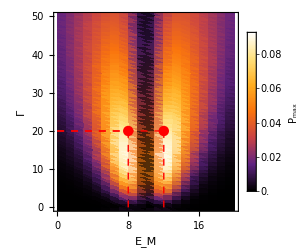
-Graphics-(a)

```mathematica
data1=Import["check221.dat"][[All,{1,2,3}]];
data2=Import["check221.dat"][[All,{1,2,4}]];
data3=Import["check221.dat"][[All,{1,2,5}]];
data4=Import["check221.dat"][[All,{1,2,6}]];
data5=Import["check221.dat"][[All,{1,2,7}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data1,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

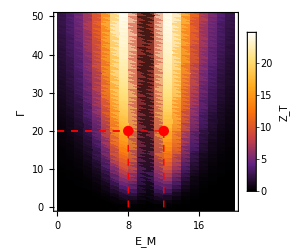
-Graphics-(d)

```mathematica
A4=Labeled[ListDensityPlot[data2,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["Z_T",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

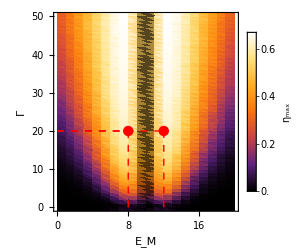
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

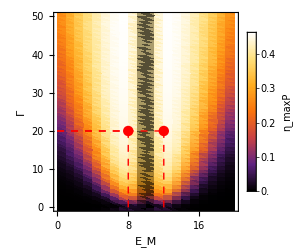
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data4,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_maxP",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2},{A3,A4}},Frame->All]
```

-Graphics-(a) | -Graphics-(b)
-Graphics-(c) | -Graphics-(d)

```mathematica
Export["fig.2.pdf",A5,ImageResolution->300]
```

fig.2.pdf

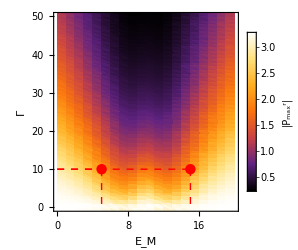
-Graphics-(a)

```mathematica
A1=Labeled[ListDensityPlot[data5,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["|P_max^r|",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,10},{5,10}},{{0,10},{15,10}},{{5,10},{5,0}},{{15,10},{15,0}}}],PointSize[0.03],Point[{{5,10},{15,10}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

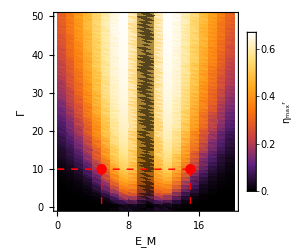
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,10},{5,10}},{{0,10},{15,10}},{{5,10},{5,0}},{{15,10},{15,0}}}],PointSize[0.03],Point[{{5,10},{15,10}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1},{A2}},Frame->All]
```

-Graphics-(a)
-Graphics-(b)

```mathematica
Export["fig4.pdf",A5,ImageResolution->300]
```

fig4.pdf

```mathematica
T1=2Abs[-((2 E^((I (G+1000 ϕ))/2000) γ (I E^((3 I (G+Gf))/2000) G+I E^((I (3 G+Gf))/2000) G+2 I E^((I (G+Gf+4000 ϕ))/2000) G-I E^((I (3 G+Gf+4000 ϕ))/2000) G+2 I E^((I (G+3 Gf+4000 ϕ))/2000) G-I E^((I (3 G+3 Gf+4000 ϕ))/2000) G+2 E^((I G)/1000+I ϕ) GM+2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM-2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM-2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+I E^((I (G+Gf))/1000) (G+I γ)+4 I E^((I Gf)/1000+2 I ϕ) (G+I γ)+I E^((I (2 G+Gf+2000 ϕ))/1000) (G+I γ)+2 E^((I G)/1000+2 I ϕ) (-I G+γ)+2 E^((I (G+2 Gf+2000 ϕ))/1000) (-I G+γ)+E^((I (2 G+Gf))/1000) (I G+γ)+E^((I (G+Gf+2000 ϕ))/1000) (I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))]^2+Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
γ=20;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[ϕ=-6.38,ϕ<=6.28,ϕ=ϕ+0.1;
{df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S = -LeT/LeV;
z0=11.5Re[ (LeV(S)^2/(kappa))/(1)];
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr=Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
list=AppendTo[list1,{GM,ϕ,P,z0,Nmax,k,Pmaxr}];
}];
},{GM,0.,20,1}];//AbsoluteTiming
list=Sort[list1];
Export["check220.dat",list]
```

{411.857,Null}

check220.dat

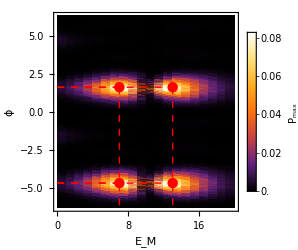
-Graphics-(a)

```mathematica
data1=Import["check220.dat"][[All,{1,2,3}]];
data2=Import["check220.dat"][[All,{1,2,4}]];
data3=Import["check220.dat"][[All,{1,2,5}]];
data4=Import["check220.dat"][[All,{1,2,6}]];
data5=Import["check220.dat"][[All,{1,2,7}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data1,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

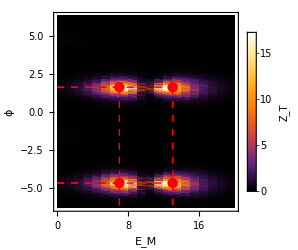
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data2,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["Z_T",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

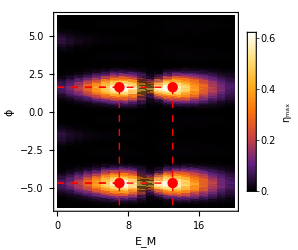
-Graphics-(d)

```mathematica
A4=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

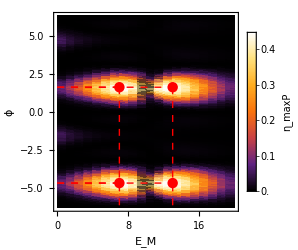
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data4,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_maxP",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2},{A3,A4}},Frame->All]
```

-Graphics-(a) | -Graphics-(b)
-Graphics-(c) | -Graphics-(d)

```mathematica
Export["fig3.pdf",A5,ImageResolution->300]
```

fig3.pdf

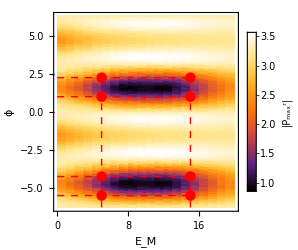
-Graphics-(a)

```mathematica
A1=Labeled[ListDensityPlot[data5,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["|P_max^r|",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1},{15,1}},{{0,2.25},{15,2.25}},{{0,-4.25},{15,-4.25}},{{0,-5.50},{15,-5.50}},{{5,-6.28},{5,2.25}},{{15,-6.28},{15,2.25}}}],PointSize[0.03],Point[{{5,1},{15,1},{5,-4.25},{15,-4.25},{5,2.25},{15,2.25},{5,-5.5},{15,-5.5}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

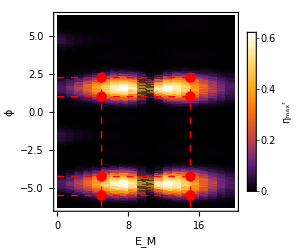
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1},{15,1}},{{0,2.25},{15,2.25}},{{0,-4.25},{15,-4.25}},{{0,-5.50},{15,-5.50}},{{5,-6.28},{5,2.25}},{{15,-6.28},{15,2.25}}}],PointSize[0.03],Point[{{5,1},{15,1},{5,-4.25},{15,-4.25},{5,2.25},{15,2.25},{5,-5.5},{15,-5.5}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1},{A2}},Frame->All]
```

-Graphics-(a)
-Graphics-(b)

```mathematica
Export["fig5.pdf",A5,ImageResolution->300]
```

fig5.pdf

```mathematica
T1=2Abs[-((2 E^((I (G+1000 ϕ))/2000) γ (I E^((3 I (G+Gf))/2000) G+I E^((I (3 G+Gf))/2000) G+2 I E^((I (G+Gf+4000 ϕ))/2000) G-I E^((I (3 G+Gf+4000 ϕ))/2000) G+2 I E^((I (G+3 Gf+4000 ϕ))/2000) G-I E^((I (3 G+3 Gf+4000 ϕ))/2000) G+2 E^((I G)/1000+I ϕ) GM+2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM-2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM-2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+I E^((I (G+Gf))/1000) (G+I γ)+4 I E^((I Gf)/1000+2 I ϕ) (G+I γ)+I E^((I (2 G+Gf+2000 ϕ))/1000) (G+I γ)+2 E^((I G)/1000+2 I ϕ) (-I G+γ)+2 E^((I (G+2 Gf+2000 ϕ))/1000) (-I G+γ)+E^((I (2 G+Gf))/1000) (I G+γ)+E^((I (G+Gf+2000 ϕ))/1000) (I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))]^2+Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
γ=20;
GM=0;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S = -LeT/LeV;
z0=11.5Re[ (LeV(S)^2/(kappa))/(1)];
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr=Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
list=AppendTo[list1,{ϕ,P,z0,Nmax,k,Pmaxr}];
},{ϕ,-6.28,6.28,0.01}];//AbsoluteTiming
list=Sort[list1];
Export["check225.dat",list]
```

{441.973,Null}

check225.dat

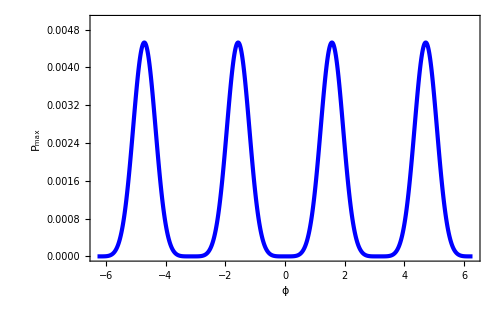
-Graphics-(a)

```mathematica
data1=Import["check225.dat"][[All,{1,2}]];
data2=Import["check225.dat"][[All,{1,3}]];
data3=Import["check225.dat"][[All,{1,4}]];
data4=Import["check225.dat"][[All,{1,5}]];
data5=Import["check225.dat"][[All,{1,6}]];
Needs["PlotLegends`"]
A1=Labeled[ListLinePlot[{data1},Frame->True,PlotRange->{{-6.28,6.28},{0,0.005}},Frame->True,FrameLabel->{Style["ϕ",25,Black],Style["P_max",25,Black]},FrameTicksStyle->Directive["Label",Black,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->500,LabelStyle->Directive[Black,15]],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

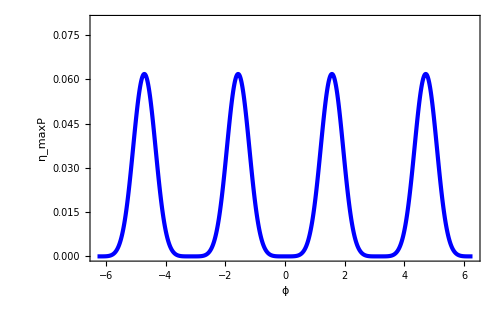
-Graphics-(b)

```mathematica
A2=Labeled[ListLinePlot[{data4},Frame->True,PlotRange->{{-6.28,6.28},{0,0.08}},Frame->True,FrameLabel->{Style["ϕ",25,Black],Style["η_maxP",25,Black]},FrameTicksStyle->Directive["Label",Black,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->500,LabelStyle->Directive[Black,15]],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

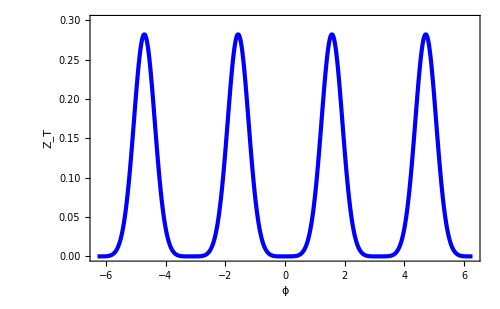
-Graphics-(c)

```mathematica
A3=Labeled[ListLinePlot[{data2},Frame->True,PlotRange->{{-6.28,6.28},{0,0.3}},Frame->True,FrameLabel->{Style["ϕ",25,Black],Style["Z_T",25,Black]},FrameTicksStyle->Directive["Label",Black,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->500,LabelStyle->Directive[Black,15]],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

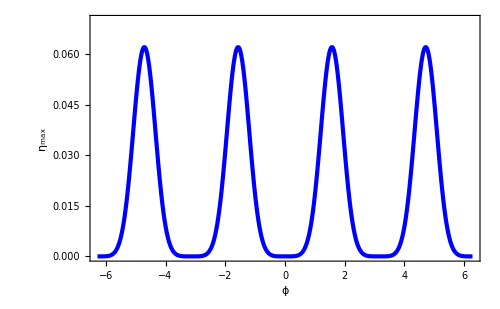
-Graphics-(d)

```mathematica
A4=Labeled[ListLinePlot[{data3},Frame->True,PlotRange->{{-6.28,6.28},{0,0.07}},Frame->True,FrameLabel->{Style["ϕ",25,Black],Style["η_max",25,Black]},FrameTicksStyle->Directive["Label",Black,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->500,LabelStyle->Directive[Black,15]],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2},{A3,A4}},Frame->All]
```

-Graphics-(a) | -Graphics-(b)
-Graphics-(c) | -Graphics-(d)

```mathematica
Export["fig8.pdf",A5,ImageResolution->300]
```

fig8.pdf

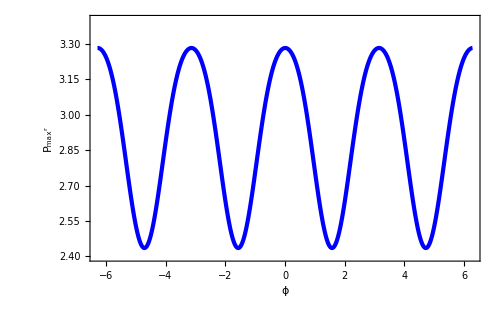
-Graphics-(a)

```mathematica
A5=Labeled[ListLinePlot[{data5},Frame->True,PlotRange->{{-6.28,6.28},{2.4,3.4}},Frame->True,FrameLabel->{Style["ϕ",25,Black],Style["P_max^r",25,Black]},FrameTicksStyle->Directive["Label",Black,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->500,LabelStyle->Directive[Black,15]],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

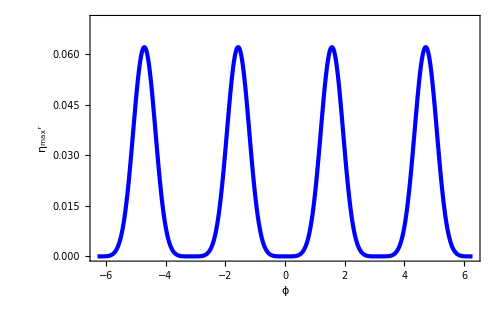
-Graphics-(b)

```mathematica
A6=Labeled[ListLinePlot[{data3},Frame->True,PlotRange->{{-6.28,6.28},{0,0.07}},Frame->True,FrameLabel->{Style["ϕ",25,Black],Style["η_max^r",25,Black]},FrameTicksStyle->Directive["Label",Black,15],PlotStyle->{Directive[AbsoluteThickness[3],Opacity[1],Blue],Directive[AbsoluteThickness[3],Opacity[1],Blue, Dashed],Directive[AbsoluteThickness[3],Opacity[1],Blue, DotDashed]},ImageSize->500,LabelStyle->Directive[Black,15]],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A5},{A6}},Frame->All]
```

-Graphics-(a)
-Graphics-(b)

```mathematica
Export["fig9.pdf",A5,ImageResolution->300]
```

fig9.pdf

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
ϕ=1.57;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[γ=-9.99,γ<=50.01,γ=γ+1;
{df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S = -LeT/LeV;
z0=11.5Re[ (LeV(S)^2/(kappa))/(1)];
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr= Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
list=AppendTo[list1,{GM,γ,P,z0,Nmax,k,Pmaxr}];
}];
},{GM,0.,20,1}];//AbsoluteTiming
list=Sort[list1];
Export["check221.dat",list]
```

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
ϕ=1.57;
kbT=1;
γ=51;
GM=7;
df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285
S = -11.5*LeT/LeV
z0=Re[ (LeV(S)^2/(kappa))/(11.5)]
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)]
k=Re[0.5*z0/(z0+2)]
Pmaxr= Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
```

0.0655943

-16.7134

24.5839

0.669861

0.462383

```mathematica
LeV
```

0.0663872

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
ϕ=1.57;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[γ=-9.99,γ<=50.01,γ=γ+1;
{df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S = -11.5*LeT/LeV;
z0=Re[ (LeV(S)^2/(kappa))/(11.5)];
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr= Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
list=AppendTo[list1,{GM,γ,P,z0,Nmax,k,Pmaxr,LeV/0.001,Re[S],Re[kappa/0.001]}];
}];
},{GM,0.,20,1}];//AbsoluteTiming
list=Sort[list1];
Export["check500.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.00185923+0. ⅈ and 3.70312×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained 0.999108+0. ⅈ and 0.000729755 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.999952+0. ⅈ and 6.7663×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.998807+0. ⅈ and 0.000936229 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -0.000902304+0. ⅈ and 0.000769452 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained 0.999512+0. ⅈ and 0.000401369 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.999827+0. ⅈ and 0.0000814889 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.00229781+0. ⅈ and 0.00186352 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.999345+0. ⅈ and 0.00034664 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -0.000902304+0. ⅈ and 0.000769452 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained -0.000959661+0. ⅈ and 0.000812461 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.99429}. NIntegrate obtained 0.000014033+0. ⅈ and 1.93835×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.00010304+0. ⅈ and 0.0000479005 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.000556271+0. ⅈ and 0.000325216 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.00229781+0. ⅈ and 0.00186352 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained -0.000959661+0. ⅈ and 0.000812461 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.000556271+0. ⅈ and 0.000325216 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.99429}. NIntegrate obtained 0.000014033+0. ⅈ and 1.93835×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.00010304+0. ⅈ and 0.0000479005 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.99429}. NIntegrate obtained 3.2896+0. ⅈ and 0.0000139452 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {1.00006}. NIntegrate obtained 1.2889×10^-6+0. ⅈ and 4.94166×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {12.8408}. NIntegrate obtained -0.0977422+0. ⅈ and 2.51286×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {12.8408}. NIntegrate obtained 3.00305+0. ⅈ and 8.15981×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {13.6319}. NIntegrate obtained -0.0554543+0. ⅈ and 1.39919×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {13.6319}. NIntegrate obtained 3.07834+0. ⅈ and 6.021×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {14.5189}. NIntegrate obtained -0.0285286+0. ⅈ and 3.25632×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {14.5189}. NIntegrate obtained 0.999931+0. ⅈ and 0.0000197788 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained -0.000114322+0. ⅈ and 0.0000988386 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained 3.28914+0. ⅈ and 0.000591263 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {16.7465}. NIntegrate obtained -0.00695186+0. ⅈ and 7.91607×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {18.6941}. NIntegrate obtained -0.00187836+0. ⅈ and 1.55306×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {16.7465}. NIntegrate obtained -0.0000286723+0. ⅈ and 0.0000187891 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {17.8477}. NIntegrate obtained -0.0000149706+0. ⅈ and 7.40189×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {18.6941}. NIntegrate obtained -8.31876×10^-6+0. ⅈ and 1.28484×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.1607}. NIntegrate obtained -7.1234×10^-6+0. ⅈ and 2.46415×10^-7 for the integral and error estimates.

{190.817,Null}

check500.dat

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

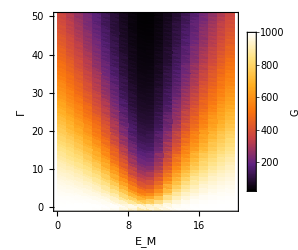
-Graphics-(a)

```mathematica
data1=Import["check500.dat"][[All,{1,2,8}]];
data2=Import["check500.dat"][[All,{1,2,9}]];
data3=Import["check500.dat"][[All,{1,2,10}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data1,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["G",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

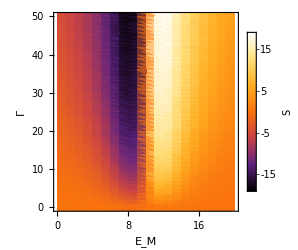
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data2,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["S",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

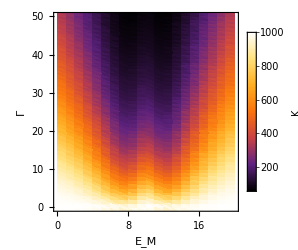
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["K",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2,A3}},Frame->All]
```

-Graphics-(a) | -Graphics-(b) | -Graphics-(c)

```mathematica
Export["fig6.pdf",A5,ImageResolution->300]
```

fig6.pdf

```mathematica
T1=Abs[(E^((I (G+Gf+1000 ϕ))/2000) p^2 (-2 b^3 E^((3 I (G+Gf))/2000) (-1+E^(2 I ϕ)) GM γ-2 b^5 E^((I (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+2 b E^((I (G+5 (Gf+400 ϕ)))/2000) (G^2-GM^2+I G γ)-a^6 E^((I (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)-b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)-E^((I Gf)/500+I ϕ) (-G^2+GM^2-2 I G γ+E^(I ϕ) GM γ+γ^2)+2 a^5 E^((I (5 G+Gf+2000 ϕ))/2000) ((1+E^((I Gf)/1000)+b E^((I (G+Gf))/2000)) G^2-(1+E^((I Gf)/1000)+b E^((I (G+Gf))/2000)) GM^2-I (1+E^((I Gf)/1000)+2 b E^((I (G+Gf))/2000)) G γ+E^((I Gf)/2000+I ϕ) (b E^((I G)/2000)+E^((I Gf)/2000)) GM γ-b E^((I (G+Gf))/2000) γ^2)+b^4 E^((I G)/500) (E^(I ϕ) (-G^2+GM^2)+E^((I Gf)/500) GM γ-E^((I Gf)/500+2 I ϕ) GM γ+E^(2 I ϕ) GM γ+E^((I Gf)/500+3 I ϕ) γ^2)+b^2 E^((I (G+Gf))/1000) (E^((I Gf)/500+I ϕ) (G^2-GM^2)+GM γ+E^((I Gf)/500+2 I ϕ) GM γ-E^(2 I ϕ) GM γ-E^(3 I ϕ) γ^2)+a^4 E^((I G)/500+I ϕ) (-((1+4 E^((I Gf)/1000)-b^2 E^((I (G+Gf))/1000)+2 b E^((I (G+Gf))/2000) (1+2 E^((I Gf)/1000))) G^2)+(1+4 E^((I Gf)/1000)-b^2 E^((I (G+Gf))/1000)+2 b E^((I (G+Gf))/2000) (1+2 E^((I Gf)/1000))) GM^2-2 I E^((I Gf)/2000) (E^((3 I Gf)/2000)+b^2 E^((I (2 G+Gf))/2000)-b E^((I G)/2000) (1+2 E^((I Gf)/1000))) G γ-E^(I ϕ) (-1-b^2 E^((I (G+Gf))/1000)+4 b E^((I (G+3 Gf))/2000)) GM γ-E^((I Gf)/1000) (2+b^2 E^((I G)/1000)+E^((I Gf)/1000)) γ^2)+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-((-1+2 b^2 E^((I G)/1000)+E^((I Gf)/500)-2 b E^((I (G+Gf))/2000)+2 b^3 E^((I (3 G+Gf))/2000)) G^2)+(-1+2 b^2 E^((I G)/1000)+E^((I Gf)/500)-2 b E^((I (G+Gf))/2000)+2 b^3 E^((I (3 G+Gf))/2000)) GM^2+I (2 b^2 E^((I G)/1000)+4 b^3 E^((I (3 G+Gf))/2000)+2 b E^((I (G+3 Gf))/2000)+(1+E^((I Gf)/1000))^2) G γ-E^(I ϕ) (1+E^((I Gf)/500)+2 b^3 E^((I (3 G+Gf))/2000)) GM γ+b E^((I (G+Gf))/2000) (1+2 b^2 E^((I G)/1000)+E^((I Gf)/1000)) γ^2)+a^2 E^((I G)/1000) (b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)+4 b^3 E^((I (3 G+Gf+2000 ϕ))/2000) ((1+E^((I Gf)/1000)) G^2-I (1+E^((I Gf)/1000)) G γ-GM (GM+E^((I Gf)/1000) GM-E^((I Gf)/1000+I ϕ) γ))+4 b E^((I (G+3 Gf+2000 ϕ))/2000) (-I G γ+E^((I Gf)/1000+I ϕ) GM γ+E^((I Gf)/1000) (G^2-GM^2-I G γ))+E^((I Gf)/1000+I ϕ) (E^((I Gf)/500) (G^2-GM^2)+E^((I Gf)/500+I ϕ) GM γ+γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+b^2 E^((I G)/1000) (2 E^(I ϕ) (G^2-GM^2)+E^((I Gf)/500) GM γ-E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^((I Gf)/500+3 I ϕ) γ^2+2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)))-2 a E^((I (G+Gf))/2000) (-b^5 E^((I (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)+b E^((I (G+3 Gf+2000 ϕ))/2000) ((2+E^((I Gf)/1000)) G^2-(2+E^((I Gf)/1000)) GM^2+E^((I Gf)/1000+I ϕ) GM γ+γ^2)+b^4 E^((I G)/500+I ϕ) ((-1+E^((I Gf)/1000)) G^2-I (-1+E^((I Gf)/1000)) G γ+GM (GM-E^((I Gf)/1000) GM+E^((I Gf)/1000+I ϕ) γ))+E^((I Gf)/1000+I ϕ) ((1+E^((I Gf)/1000)) G^2+I (1+E^((I Gf)/1000)) G γ-GM (GM+E^((I Gf)/1000) GM+E^(I ϕ) γ))+b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ-E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2+I G γ))+b^3 E^((I (3 G+Gf))/2000) (E^((I Gf)/1000) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/1000+3 I ϕ) γ^2+E^(I ϕ) (2 G^2-2 GM^2+γ^2)))))/(b^2 E^((I (G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ+b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ-2 a^7 E^((I (7 G+3 Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+2 a^5 E^((I (5 G+Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) GM^2-I (1+E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G γ)+a^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+b^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+E^((I Gf)/500+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+b^4 E^((I G)/500) (E^((I Gf)/250+2 I ϕ) (-G^2+GM^2)+E^(2 I ϕ) (-G^2+GM^2)+E^((I Gf)/500) γ^2+E^((I Gf)/500+4 I ϕ) γ^2)+a^6 E^((I (3 G+Gf+2000 ϕ))/1000) (γ (2 I G+γ)+E^((I Gf)/500) γ (2 I G+γ)-4 b^2 E^((I (G+Gf))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 E^((I G)/500+I ϕ) (E^((I Gf)/250+I ϕ) (-G^2+GM^2)+E^(I ϕ) (-G^2+GM^2)+b^2 E^((I (G+Gf))/1000) GM γ-b^2 E^((I (G+3 Gf))/1000) GM γ-b^2 E^((I (G+Gf+2000 ϕ))/1000) GM γ+b^2 E^((I (G+3 Gf+2000 ϕ))/1000) GM γ-2 I b^2 E^((I (G+Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 I b^2 E^((I (G+3 Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 E^((I Gf)/500+I ϕ) γ^2+6 b^4 E^(1/500 I (G+Gf+500 ϕ)) (G^2-GM^2-2 I G γ-γ^2)-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-2 E^((3 I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 E^((I (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-3 b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+E^(I ϕ) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)) GM^2+I (1+E^((I Gf)/1000)+E^((I Gf)/500)) G γ)-b^2 E^((I G)/1000) (-2 I E^((I Gf)/1000+I ϕ) G γ-2 I E^((I Gf)/500+I ϕ) G γ+E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+2 E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+2 E^(I ϕ) (G^2-GM^2-I G γ)))+2 a E^((I (G+Gf+2000 ϕ))/2000) (b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)-E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) (G^2-GM^2+I G γ)+b^4 E^((I G)/500) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2-I G γ))-b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2+I G γ)+E^(I ϕ) (G^2-GM^2+I G γ)))+a^2 E^((I G)/1000+I ϕ) (-4 b^6 E^((I (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 b^2 E^((I G)/1000+I ϕ) ((1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) G^2-(1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) GM^2+E^((I Gf)/1000) (1+E^((I Gf)/500)) γ^2)+E^((I Gf)/1000+I ϕ) (γ (-2 I G+γ)+E^((I Gf)/500) γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 E^((I (2 G+Gf))/1000) (2 GM γ-2 E^((I Gf)/500) GM γ+2 E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^(I ϕ) (-2 I G-γ) γ-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2))))]^2+Abs[-((E^((I (G+Gf+2000 ϕ))/2000) p^2 γ (E^((3 I Gf)/2000+I ϕ) GM+a^6 E^((I (6 G+3 Gf+2000 ϕ))/2000) GM+b^6 E^((I (6 G+3 Gf+2000 ϕ))/2000) GM+b^3 E^((3 I G)/2000+I ϕ) (-1+E^((I Gf)/1000))^2 (1+E^((I Gf)/1000)) GM-a^5 E^((I (5 G+2 Gf+2000 ϕ))/2000) (1+E^((I Gf)/1000)+2 b E^((I (G+Gf))/2000)) GM+I b^4 E^((I (4 G+Gf))/2000) (G+E^((I Gf)/500+2 I ϕ) G+I E^((I Gf)/1000+I ϕ) GM)+I b^2 E^((I (2 G+Gf))/2000) (E^((I Gf)/500) G+E^(2 I ϕ) G+I E^((I Gf)/1000+I ϕ) GM)-a^2 E^((I G)/1000) (b^4 E^((I (4 G+3 Gf+2000 ϕ))/2000) GM+2 b^3 E^((I (3 G+2 Gf+2000 ϕ))/2000) (1+E^((I Gf)/1000)) GM+E^((I Gf)/2000+I ϕ) (1-E^((I Gf)/1000)+E^((I Gf)/500)) GM+I b^2 E^((I (2 G+Gf))/2000) ((1+2 E^((I Gf)/1000)+2 E^((I Gf)/1000+2 I ϕ)+E^((I Gf)/500+2 I ϕ)) G+I E^(I ϕ) (1+E^((I Gf)/500)) GM)+b E^((I G)/2000) (E^((I Gf)/1000+I ϕ) GM+E^((I Gf)/500+I ϕ) GM+E^((3 I Gf)/1000+I ϕ) GM+E^(I ϕ) GM+E^((I Gf)/500) (-I G-γ)+E^((I Gf)/1000+2 I ϕ) (-I G-γ)+I E^((I Gf)/1000) (G+I γ)+I E^((I Gf)/500+2 I ϕ) (G+I γ)))+I b E^((I (G+2 Gf))/2000) (E^((I Gf)/1000)+E^(2 I ϕ)) (G+I γ)+b^5 E^((I (5 G+2 Gf))/2000) (1+E^((I Gf)/1000+2 I ϕ)) (I G+γ)+a^3 E^((3 I G)/2000) (4 b^3 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+E^(I ϕ) (1+E^((I Gf)/1000)+E^((I Gf)/500)+E^((3 I Gf)/1000)) GM+b E^((I (G+Gf))/2000) (I (1+E^((I Gf)/1000)) (1+E^((I Gf)/1000+2 I ϕ)) G+E^(I ϕ) (-1+E^((I Gf)/1000))^2 GM)+2 b^2 E^((I (G+Gf))/1000) (1+E^((I Gf)/1000+2 I ϕ)) (I G+γ))-a^4 E^((I (4 G+Gf))/2000) (b^2 E^((I (G+Gf+1000 ϕ))/1000) GM+E^(I ϕ) (1-E^((I Gf)/1000)+E^((I Gf)/500)) GM+b E^((I (G+Gf))/2000) (I (1+E^((I Gf)/1000+2 I ϕ)) G-2 E^((I Gf)/1000+I ϕ) GM-2 E^(I ϕ) GM+γ+E^((I Gf)/1000+2 I ϕ) γ))-a E^((I G)/2000) (2 b^5 E^((I (5 G+3 Gf+2000 ϕ))/2000) GM+E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) GM+I b E^((I (G+Gf))/2000) (E^((I Gf)/1000) G+E^((I Gf)/500) G+E^((I Gf)/1000+2 I ϕ) G+E^(2 I ϕ) G+I E^((I Gf)/500+I ϕ) GM+I E^(I ϕ) GM)+b^3 E^((I (3 G+Gf))/2000) (-1+E^((I Gf)/1000)) (I (-1+E^((I Gf)/1000+2 I ϕ)) G+E^(I ϕ) (-1+E^((I Gf)/1000)) GM)+b^4 E^((I (2 G+Gf))/1000) (2 I (1+E^((I Gf)/1000+2 I ϕ)) G-E^((I Gf)/1000+I ϕ) GM-E^(I ϕ) GM+2 γ+2 E^((I Gf)/1000+2 I ϕ) γ)+b^2 E^((I G)/1000) (-E^((I Gf)/1000+I ϕ) GM-E^((I Gf)/500+I ϕ) GM+E^((3 I Gf)/1000+I ϕ) GM+E^(I ϕ) GM+E^((I Gf)/1000) (-I G+γ)+E^((I Gf)/500+2 I ϕ) (-I G+γ)+E^((I Gf)/500) (I G+γ)+E^((I Gf)/1000+2 I ϕ) (I G+γ)))))/(b^2 E^((I (G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ+b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ-2 a^7 E^((I (7 G+3 Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+2 a^5 E^((I (5 G+Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) GM^2-I (1+E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G γ)+a^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+b^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+E^((I Gf)/500+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+b^4 E^((I G)/500) (E^((I Gf)/250+2 I ϕ) (-G^2+GM^2)+E^(2 I ϕ) (-G^2+GM^2)+E^((I Gf)/500) γ^2+E^((I Gf)/500+4 I ϕ) γ^2)+a^6 E^((I (3 G+Gf+2000 ϕ))/1000) (γ (2 I G+γ)+E^((I Gf)/500) γ (2 I G+γ)-4 b^2 E^((I (G+Gf))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 E^((I G)/500+I ϕ) (E^((I Gf)/250+I ϕ) (-G^2+GM^2)+E^(I ϕ) (-G^2+GM^2)+b^2 E^((I (G+Gf))/1000) GM γ-b^2 E^((I (G+3 Gf))/1000) GM γ-b^2 E^((I (G+Gf+2000 ϕ))/1000) GM γ+b^2 E^((I (G+3 Gf+2000 ϕ))/1000) GM γ-2 I b^2 E^((I (G+Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 I b^2 E^((I (G+3 Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 E^((I Gf)/500+I ϕ) γ^2+6 b^4 E^(1/500 I (G+Gf+500 ϕ)) (G^2-GM^2-2 I G γ-γ^2)-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-2 E^((3 I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 E^((I (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-3 b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+E^(I ϕ) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)) GM^2+I (1+E^((I Gf)/1000)+E^((I Gf)/500)) G γ)-b^2 E^((I G)/1000) (-2 I E^((I Gf)/1000+I ϕ) G γ-2 I E^((I Gf)/500+I ϕ) G γ+E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+2 E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+2 E^(I ϕ) (G^2-GM^2-I G γ)))+2 a E^((I (G+Gf+2000 ϕ))/2000) (b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)-E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) (G^2-GM^2+I G γ)+b^4 E^((I G)/500) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2-I G γ))-b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2+I G γ)+E^(I ϕ) (G^2-GM^2+I G γ)))+a^2 E^((I G)/1000+I ϕ) (-4 b^6 E^((I (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 b^2 E^((I G)/1000+I ϕ) ((1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) G^2-(1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) GM^2+E^((I Gf)/1000) (1+E^((I Gf)/500)) γ^2)+E^((I Gf)/1000+I ϕ) (γ (-2 I G+γ)+E^((I Gf)/500) γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 E^((I (2 G+Gf))/1000) (2 GM γ-2 E^((I Gf)/500) GM γ+2 E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^(I ϕ) (-2 I G-γ) γ-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)))))]^2;
a=1/2(√(1/2)-1);
b=1/2(√(1/2)+1);
p=1/2;
Gf=10;
ϕ=1.57;
kbT=1;
GM=7;
γ=51;
df=(E^(((G-10)/kbT))/((1+E^((G-10)/kbT))^2 kbT));
LeTt=(((G-(Gf))/kbT)^(1)) (T1) (df);
LeVv=(((G-(Gf))/kbT)^(0)) (T1) (df);
LhVv=(((G-(Gf))/kbT)^(1)) (T1) (df);
LhTt=(((G-(Gf))/kbT)^(2)) (T1) (df);
LeV=NIntegrate[LeVv,{G,-Infinity,Infinity}];
LeT=NIntegrate[LeTt,{G,-Infinity,Infinity}];
LhV=NIntegrate[LhVv,{G,-Infinity,Infinity}];
LhT=NIntegrate[LhTt,{G,-Infinity,Infinity}];
P=Re[(1/(4*1))*((LeT)^2)/LeV];
kappa=((LeV*LhT-LhV*LeT)/(LeV))/3.285;
S=-11.5*LeT/LeV;
z0=Re[(LeV (S)^2/(kappa))/(11.5)];
Nmax=Re[(Sqrt[z0+1]-1)/(Sqrt[z0+1]+1)]
```

0.685253

```mathematica
z0
```

27.6687

```mathematica
T1=Abs[(E^((I (G+Gf+1000 ϕ))/2000) p^2 (-2 b^3 E^((3 I (G+Gf))/2000) (-1+E^(2 I ϕ)) GM γ-2 b^5 E^((I (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+2 b E^((I (G+5 (Gf+400 ϕ)))/2000) (G^2-GM^2+I G γ)-a^6 E^((I (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)-b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)-E^((I Gf)/500+I ϕ) (-G^2+GM^2-2 I G γ+E^(I ϕ) GM γ+γ^2)+2 a^5 E^((I (5 G+Gf+2000 ϕ))/2000) ((1+E^((I Gf)/1000)+b E^((I (G+Gf))/2000)) G^2-(1+E^((I Gf)/1000)+b E^((I (G+Gf))/2000)) GM^2-I (1+E^((I Gf)/1000)+2 b E^((I (G+Gf))/2000)) G γ+E^((I Gf)/2000+I ϕ) (b E^((I G)/2000)+E^((I Gf)/2000)) GM γ-b E^((I (G+Gf))/2000) γ^2)+b^4 E^((I G)/500) (E^(I ϕ) (-G^2+GM^2)+E^((I Gf)/500) GM γ-E^((I Gf)/500+2 I ϕ) GM γ+E^(2 I ϕ) GM γ+E^((I Gf)/500+3 I ϕ) γ^2)+b^2 E^((I (G+Gf))/1000) (E^((I Gf)/500+I ϕ) (G^2-GM^2)+GM γ+E^((I Gf)/500+2 I ϕ) GM γ-E^(2 I ϕ) GM γ-E^(3 I ϕ) γ^2)+a^4 E^((I G)/500+I ϕ) (-((1+4 E^((I Gf)/1000)-b^2 E^((I (G+Gf))/1000)+2 b E^((I (G+Gf))/2000) (1+2 E^((I Gf)/1000))) G^2)+(1+4 E^((I Gf)/1000)-b^2 E^((I (G+Gf))/1000)+2 b E^((I (G+Gf))/2000) (1+2 E^((I Gf)/1000))) GM^2-2 I E^((I Gf)/2000) (E^((3 I Gf)/2000)+b^2 E^((I (2 G+Gf))/2000)-b E^((I G)/2000) (1+2 E^((I Gf)/1000))) G γ-E^(I ϕ) (-1-b^2 E^((I (G+Gf))/1000)+4 b E^((I (G+3 Gf))/2000)) GM γ-E^((I Gf)/1000) (2+b^2 E^((I G)/1000)+E^((I Gf)/1000)) γ^2)+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-((-1+2 b^2 E^((I G)/1000)+E^((I Gf)/500)-2 b E^((I (G+Gf))/2000)+2 b^3 E^((I (3 G+Gf))/2000)) G^2)+(-1+2 b^2 E^((I G)/1000)+E^((I Gf)/500)-2 b E^((I (G+Gf))/2000)+2 b^3 E^((I (3 G+Gf))/2000)) GM^2+I (2 b^2 E^((I G)/1000)+4 b^3 E^((I (3 G+Gf))/2000)+2 b E^((I (G+3 Gf))/2000)+(1+E^((I Gf)/1000))^2) G γ-E^(I ϕ) (1+E^((I Gf)/500)+2 b^3 E^((I (3 G+Gf))/2000)) GM γ+b E^((I (G+Gf))/2000) (1+2 b^2 E^((I G)/1000)+E^((I Gf)/1000)) γ^2)+a^2 E^((I G)/1000) (b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)+4 b^3 E^((I (3 G+Gf+2000 ϕ))/2000) ((1+E^((I Gf)/1000)) G^2-I (1+E^((I Gf)/1000)) G γ-GM (GM+E^((I Gf)/1000) GM-E^((I Gf)/1000+I ϕ) γ))+4 b E^((I (G+3 Gf+2000 ϕ))/2000) (-I G γ+E^((I Gf)/1000+I ϕ) GM γ+E^((I Gf)/1000) (G^2-GM^2-I G γ))+E^((I Gf)/1000+I ϕ) (E^((I Gf)/500) (G^2-GM^2)+E^((I Gf)/500+I ϕ) GM γ+γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+b^2 E^((I G)/1000) (2 E^(I ϕ) (G^2-GM^2)+E^((I Gf)/500) GM γ-E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^((I Gf)/500+3 I ϕ) γ^2+2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)))-2 a E^((I (G+Gf))/2000) (-b^5 E^((I (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)+b E^((I (G+3 Gf+2000 ϕ))/2000) ((2+E^((I Gf)/1000)) G^2-(2+E^((I Gf)/1000)) GM^2+E^((I Gf)/1000+I ϕ) GM γ+γ^2)+b^4 E^((I G)/500+I ϕ) ((-1+E^((I Gf)/1000)) G^2-I (-1+E^((I Gf)/1000)) G γ+GM (GM-E^((I Gf)/1000) GM+E^((I Gf)/1000+I ϕ) γ))+E^((I Gf)/1000+I ϕ) ((1+E^((I Gf)/1000)) G^2+I (1+E^((I Gf)/1000)) G γ-GM (GM+E^((I Gf)/1000) GM+E^(I ϕ) γ))+b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ-E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2+I G γ))+b^3 E^((I (3 G+Gf))/2000) (E^((I Gf)/1000) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/1000+3 I ϕ) γ^2+E^(I ϕ) (2 G^2-2 GM^2+γ^2)))))/(b^2 E^((I (G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ+b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ-2 a^7 E^((I (7 G+3 Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+2 a^5 E^((I (5 G+Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) GM^2-I (1+E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G γ)+a^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+b^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+E^((I Gf)/500+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+b^4 E^((I G)/500) (E^((I Gf)/250+2 I ϕ) (-G^2+GM^2)+E^(2 I ϕ) (-G^2+GM^2)+E^((I Gf)/500) γ^2+E^((I Gf)/500+4 I ϕ) γ^2)+a^6 E^((I (3 G+Gf+2000 ϕ))/1000) (γ (2 I G+γ)+E^((I Gf)/500) γ (2 I G+γ)-4 b^2 E^((I (G+Gf))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 E^((I G)/500+I ϕ) (E^((I Gf)/250+I ϕ) (-G^2+GM^2)+E^(I ϕ) (-G^2+GM^2)+b^2 E^((I (G+Gf))/1000) GM γ-b^2 E^((I (G+3 Gf))/1000) GM γ-b^2 E^((I (G+Gf+2000 ϕ))/1000) GM γ+b^2 E^((I (G+3 Gf+2000 ϕ))/1000) GM γ-2 I b^2 E^((I (G+Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 I b^2 E^((I (G+3 Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 E^((I Gf)/500+I ϕ) γ^2+6 b^4 E^(1/500 I (G+Gf+500 ϕ)) (G^2-GM^2-2 I G γ-γ^2)-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-2 E^((3 I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 E^((I (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-3 b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+E^(I ϕ) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)) GM^2+I (1+E^((I Gf)/1000)+E^((I Gf)/500)) G γ)-b^2 E^((I G)/1000) (-2 I E^((I Gf)/1000+I ϕ) G γ-2 I E^((I Gf)/500+I ϕ) G γ+E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+2 E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+2 E^(I ϕ) (G^2-GM^2-I G γ)))+2 a E^((I (G+Gf+2000 ϕ))/2000) (b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)-E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) (G^2-GM^2+I G γ)+b^4 E^((I G)/500) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2-I G γ))-b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2+I G γ)+E^(I ϕ) (G^2-GM^2+I G γ)))+a^2 E^((I G)/1000+I ϕ) (-4 b^6 E^((I (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 b^2 E^((I G)/1000+I ϕ) ((1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) G^2-(1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) GM^2+E^((I Gf)/1000) (1+E^((I Gf)/500)) γ^2)+E^((I Gf)/1000+I ϕ) (γ (-2 I G+γ)+E^((I Gf)/500) γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 E^((I (2 G+Gf))/1000) (2 GM γ-2 E^((I Gf)/500) GM γ+2 E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^(I ϕ) (-2 I G-γ) γ-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2))))]^2+Abs[-((E^((I (G+Gf+2000 ϕ))/2000) p^2 γ (E^((3 I Gf)/2000+I ϕ) GM+a^6 E^((I (6 G+3 Gf+2000 ϕ))/2000) GM+b^6 E^((I (6 G+3 Gf+2000 ϕ))/2000) GM+b^3 E^((3 I G)/2000+I ϕ) (-1+E^((I Gf)/1000))^2 (1+E^((I Gf)/1000)) GM-a^5 E^((I (5 G+2 Gf+2000 ϕ))/2000) (1+E^((I Gf)/1000)+2 b E^((I (G+Gf))/2000)) GM+I b^4 E^((I (4 G+Gf))/2000) (G+E^((I Gf)/500+2 I ϕ) G+I E^((I Gf)/1000+I ϕ) GM)+I b^2 E^((I (2 G+Gf))/2000) (E^((I Gf)/500) G+E^(2 I ϕ) G+I E^((I Gf)/1000+I ϕ) GM)-a^2 E^((I G)/1000) (b^4 E^((I (4 G+3 Gf+2000 ϕ))/2000) GM+2 b^3 E^((I (3 G+2 Gf+2000 ϕ))/2000) (1+E^((I Gf)/1000)) GM+E^((I Gf)/2000+I ϕ) (1-E^((I Gf)/1000)+E^((I Gf)/500)) GM+I b^2 E^((I (2 G+Gf))/2000) ((1+2 E^((I Gf)/1000)+2 E^((I Gf)/1000+2 I ϕ)+E^((I Gf)/500+2 I ϕ)) G+I E^(I ϕ) (1+E^((I Gf)/500)) GM)+b E^((I G)/2000) (E^((I Gf)/1000+I ϕ) GM+E^((I Gf)/500+I ϕ) GM+E^((3 I Gf)/1000+I ϕ) GM+E^(I ϕ) GM+E^((I Gf)/500) (-I G-γ)+E^((I Gf)/1000+2 I ϕ) (-I G-γ)+I E^((I Gf)/1000) (G+I γ)+I E^((I Gf)/500+2 I ϕ) (G+I γ)))+I b E^((I (G+2 Gf))/2000) (E^((I Gf)/1000)+E^(2 I ϕ)) (G+I γ)+b^5 E^((I (5 G+2 Gf))/2000) (1+E^((I Gf)/1000+2 I ϕ)) (I G+γ)+a^3 E^((3 I G)/2000) (4 b^3 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+E^(I ϕ) (1+E^((I Gf)/1000)+E^((I Gf)/500)+E^((3 I Gf)/1000)) GM+b E^((I (G+Gf))/2000) (I (1+E^((I Gf)/1000)) (1+E^((I Gf)/1000+2 I ϕ)) G+E^(I ϕ) (-1+E^((I Gf)/1000))^2 GM)+2 b^2 E^((I (G+Gf))/1000) (1+E^((I Gf)/1000+2 I ϕ)) (I G+γ))-a^4 E^((I (4 G+Gf))/2000) (b^2 E^((I (G+Gf+1000 ϕ))/1000) GM+E^(I ϕ) (1-E^((I Gf)/1000)+E^((I Gf)/500)) GM+b E^((I (G+Gf))/2000) (I (1+E^((I Gf)/1000+2 I ϕ)) G-2 E^((I Gf)/1000+I ϕ) GM-2 E^(I ϕ) GM+γ+E^((I Gf)/1000+2 I ϕ) γ))-a E^((I G)/2000) (2 b^5 E^((I (5 G+3 Gf+2000 ϕ))/2000) GM+E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) GM+I b E^((I (G+Gf))/2000) (E^((I Gf)/1000) G+E^((I Gf)/500) G+E^((I Gf)/1000+2 I ϕ) G+E^(2 I ϕ) G+I E^((I Gf)/500+I ϕ) GM+I E^(I ϕ) GM)+b^3 E^((I (3 G+Gf))/2000) (-1+E^((I Gf)/1000)) (I (-1+E^((I Gf)/1000+2 I ϕ)) G+E^(I ϕ) (-1+E^((I Gf)/1000)) GM)+b^4 E^((I (2 G+Gf))/1000) (2 I (1+E^((I Gf)/1000+2 I ϕ)) G-E^((I Gf)/1000+I ϕ) GM-E^(I ϕ) GM+2 γ+2 E^((I Gf)/1000+2 I ϕ) γ)+b^2 E^((I G)/1000) (-E^((I Gf)/1000+I ϕ) GM-E^((I Gf)/500+I ϕ) GM+E^((3 I Gf)/1000+I ϕ) GM+E^(I ϕ) GM+E^((I Gf)/1000) (-I G+γ)+E^((I Gf)/500+2 I ϕ) (-I G+γ)+E^((I Gf)/500) (I G+γ)+E^((I Gf)/1000+2 I ϕ) (I G+γ)))))/(b^2 E^((I (G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ+b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ-2 a^7 E^((I (7 G+3 Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+2 a^5 E^((I (5 G+Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) GM^2-I (1+E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G γ)+a^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+b^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+E^((I Gf)/500+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+b^4 E^((I G)/500) (E^((I Gf)/250+2 I ϕ) (-G^2+GM^2)+E^(2 I ϕ) (-G^2+GM^2)+E^((I Gf)/500) γ^2+E^((I Gf)/500+4 I ϕ) γ^2)+a^6 E^((I (3 G+Gf+2000 ϕ))/1000) (γ (2 I G+γ)+E^((I Gf)/500) γ (2 I G+γ)-4 b^2 E^((I (G+Gf))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 E^((I G)/500+I ϕ) (E^((I Gf)/250+I ϕ) (-G^2+GM^2)+E^(I ϕ) (-G^2+GM^2)+b^2 E^((I (G+Gf))/1000) GM γ-b^2 E^((I (G+3 Gf))/1000) GM γ-b^2 E^((I (G+Gf+2000 ϕ))/1000) GM γ+b^2 E^((I (G+3 Gf+2000 ϕ))/1000) GM γ-2 I b^2 E^((I (G+Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 I b^2 E^((I (G+3 Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 E^((I Gf)/500+I ϕ) γ^2+6 b^4 E^(1/500 I (G+Gf+500 ϕ)) (G^2-GM^2-2 I G γ-γ^2)-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-2 E^((3 I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 E^((I (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-3 b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+E^(I ϕ) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)) GM^2+I (1+E^((I Gf)/1000)+E^((I Gf)/500)) G γ)-b^2 E^((I G)/1000) (-2 I E^((I Gf)/1000+I ϕ) G γ-2 I E^((I Gf)/500+I ϕ) G γ+E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+2 E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+2 E^(I ϕ) (G^2-GM^2-I G γ)))+2 a E^((I (G+Gf+2000 ϕ))/2000) (b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)-E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) (G^2-GM^2+I G γ)+b^4 E^((I G)/500) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2-I G γ))-b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2+I G γ)+E^(I ϕ) (G^2-GM^2+I G γ)))+a^2 E^((I G)/1000+I ϕ) (-4 b^6 E^((I (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 b^2 E^((I G)/1000+I ϕ) ((1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) G^2-(1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) GM^2+E^((I Gf)/1000) (1+E^((I Gf)/500)) γ^2)+E^((I Gf)/1000+I ϕ) (γ (-2 I G+γ)+E^((I Gf)/500) γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 E^((I (2 G+Gf))/1000) (2 GM γ-2 E^((I Gf)/500) GM γ+2 E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^(I ϕ) (-2 I G-γ) γ-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)))))]^2;
a=1/2(√(1/2)-1);
b=1/2(√(1/2)+1);
p=1/2;
Gf=10;
ϕ=1.57;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{For[γ=-9.99,γ<=50.01,γ=γ+1;
{df=(E^(((G-10)/kbT))/((1+E^((G-10)/kbT))^2 kbT));
LeTt=(((G-(Gf))/kbT)^(1)) (T1) (df);
LeVv=(((G-(Gf))/kbT)^(0)) (T1) (df);
LhVv=(((G-(Gf))/kbT)^(1)) (T1) (df);
LhTt=(((G-(Gf))/kbT)^(2)) (T1) (df);
LeV=NIntegrate[LeVv,{G,-Infinity,Infinity}];
LeT=NIntegrate[LeTt,{G,-Infinity,Infinity}];
LhV=NIntegrate[LhVv,{G,-Infinity,Infinity}];
LhT=NIntegrate[LhTt,{G,-Infinity,Infinity}];
P=Re[(1/(4*1))*((LeT)^2)/LeV];
kappa=((LeV*LhT-LhV*LeT)/(LeV))/3.285;
S=-11.5*LeT/LeV;
z0=Re[(LeV (S)^2/(kappa))/(11.5)];
Nmax=Re[(Sqrt[z0+1]-1)/(Sqrt[z0+1]+1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr=Re[Sqrt[(LhT) (LeV*LhT-LhV*LeT)/(LeV)]];
list=AppendTo[list1,{GM,γ,P,z0,Nmax,k,Pmaxr,Re[LeV/0.001],Re[S],Re[kappa/0.001]}];}];},{GM,0.,20,1}];//AbsoluteTiming
list=Sort[list1];
Export["check421.dat",list]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained 0.993694+0. ⅈ and 0.00282526 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.98861+0. ⅈ and 0.00273508 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.99865+0. ⅈ and 5.70255×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained -0.0104766+0. ⅈ and 0.00577277 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.000519097+0. ⅈ and 0.000134037 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.0028557+0. ⅈ and 0.0000334587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.994778+0. ⅈ and 0.000522811 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {11.8025}. NIntegrate obtained -0.0104766+0. ⅈ and 0.00577277 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {9.89546}. NIntegrate obtained 0.000519097+0. ⅈ and 0.000134037 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained 0.989584+0. ⅈ and 0.00427341 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {5.91966}. NIntegrate obtained 0.0028557+0. ⅈ and 0.0000334587 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.000367002+0. ⅈ and 1.91146×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.00938061+0. ⅈ and 0.000948693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -0.00906764+0. ⅈ and 0.00446552 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.000367002+0. ⅈ and 1.91146×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {7.98371}. NIntegrate obtained 0.00938061+0. ⅈ and 0.000948693 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 3.28378+0. ⅈ and 0.0000101275 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {10.9092}. NIntegrate obtained -0.00906764+0. ⅈ and 0.00446552 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {12.8408}. NIntegrate obtained 0.997486+0. ⅈ and 0.00011044 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {12.8408}. NIntegrate obtained -0.00463953+0. ⅈ and 0.000332121 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {13.6319}. NIntegrate obtained 0.998044+0. ⅈ and 0.000524019 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {12.8408}. NIntegrate obtained -0.00463953+0. ⅈ and 0.000332121 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {13.6319}. NIntegrate obtained -0.00418378+0. ⅈ and 0.00210886 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {13.6319}. NIntegrate obtained -0.00418378+0. ⅈ and 0.00210886 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.00025}. NIntegrate obtained 2.46336×10^-6+0. ⅈ and 4.95944×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {14.5189}. NIntegrate obtained 0.998734+0. ⅈ and 0.0000226984 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.00025}. NIntegrate obtained 2.46336×10^-6+0. ⅈ and 4.95944×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {14.5189}. NIntegrate obtained -0.00193817+0. ⅈ and 0.000158386 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {14.5189}. NIntegrate obtained -0.00193817+0. ⅈ and 0.000158386 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained 0.998951+0. ⅈ and 0.000071486 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {15.8089}. NIntegrate obtained -0.00115508+0. ⅈ and 0.000437725 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {16.7465}. NIntegrate obtained -0.000649642+0. ⅈ and 0.000138101 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {17.8477}. NIntegrate obtained 0.999112+0. ⅈ and 0.0000110519 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {17.8477}. NIntegrate obtained -0.000461044+0. ⅈ and 0.0000952193 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {18.6941}. NIntegrate obtained -0.000353854+0. ⅈ and 0.0000264252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.6494}. NIntegrate obtained -0.000311663+0. ⅈ and 8.67773×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {18.6941}. NIntegrate obtained -0.000353854+0. ⅈ and 0.0000264252 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.6494}. NIntegrate obtained -0.000311663+0. ⅈ and 8.67773×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {18.6941}. NIntegrate obtained 3.28649+0. ⅈ and 0.000233613 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {19.6494}. NIntegrate obtained 3.2868+0. ⅈ and 0.0000908548 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{3204.58,Null}

check421.dat

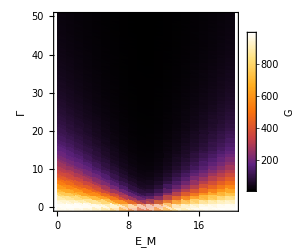
-Graphics-(a)

```mathematica
data1=Import["check421.dat"][[All,{1,2,8}]];
data2=Import["check421.dat"][[All,{1,2,9}]];
data3=Import["check421.dat"][[All,{1,2,10}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data1,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["G",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

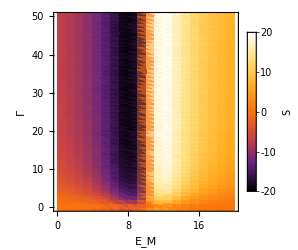
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data2,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["S",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

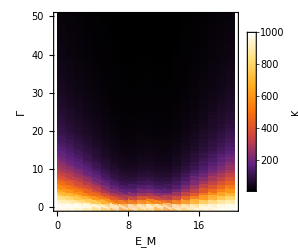
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["K",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2,A3}},Frame->All]
```

-Graphics-(a) | -Graphics-(b) | -Graphics-(c)

```mathematica
Export["fig11.pdf",A5,ImageResolution->300]
```

fig11.pdf

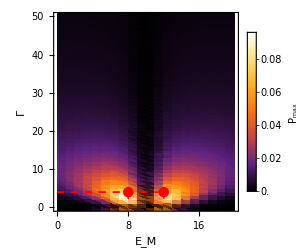
-Graphics-(a)

```mathematica
data1=Import["check421.dat"][[All,{1,2,3}]];
data2=Import["check421.dat"][[All,{1,2,4}]];
data3=Import["check421.dat"][[All,{1,2,5}]];
data4=Import["check421.dat"][[All,{1,2,6}]];
data5=Import["check421.dat"][[All,{1,2,7}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data1,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

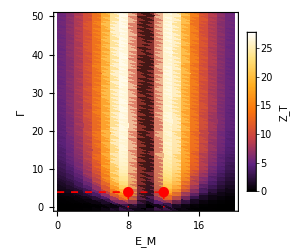
-Graphics-(d)

```mathematica
A4=Labeled[ListDensityPlot[data2,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["Z_T",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

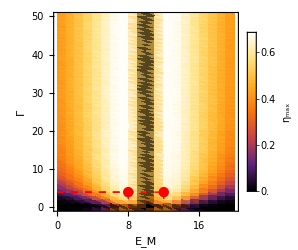
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

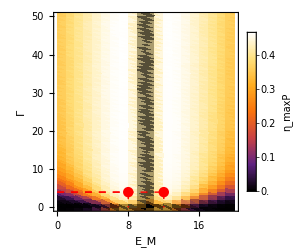
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data4,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_maxP",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2},{A3,A4}},Frame->All]
```

-Graphics-(a) | -Graphics-(b)
-Graphics-(c) | -Graphics-(d)

```mathematica
Export["fig9.pdf",A5,ImageResolution->300]
```

fig9.pdf

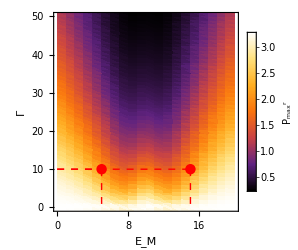
-Graphics-(a)

```mathematica
data5=Import["check221.dat"][[All,{1,2,7}]];
data6=Import["check221.dat"][[All,{1,2,5}]];
data7=Import["check421.dat"][[All,{1,2,7}]];
data8=Import["check421.dat"][[All,{1,2,5}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data5,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,10},{5,10}},{{0,10},{15,10}},{{5,10},{5,0}},{{15,10},{15,0}}}],PointSize[0.03],Point[{{5,10},{15,10}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

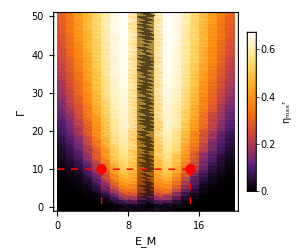
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data6,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,10},{5,10}},{{0,10},{15,10}},{{5,10},{5,0}},{{15,10},{15,0}}}],PointSize[0.03],Point[{{5,10},{15,10}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

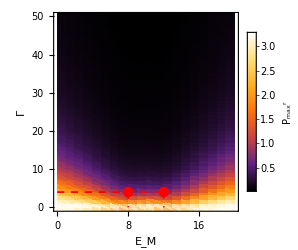
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data7,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

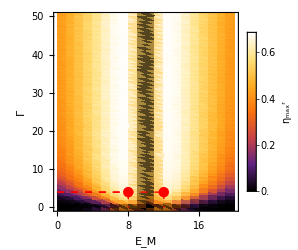
-Graphics-(d)

```mathematica
A4=Labeled[ListDensityPlot[data8,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2},{A3,A4}},Frame->All]
```

-Graphics-(a) | -Graphics-(b)
-Graphics-(c) | -Graphics-(d)

```mathematica
Export["fig10.pdf",A5,ImageResolution->300]
```

fig10.pdf

```mathematica
A3=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

-Graphics-(d)

```mathematica
A3=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,4},{8,4}},{{0,4},{12,4}},{{8,4},{8,0}},{{12,4},{12,0}}}],PointSize[0.03],Point[{{8,4},{12,4}}]}],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fig6.pdf"]]]
```

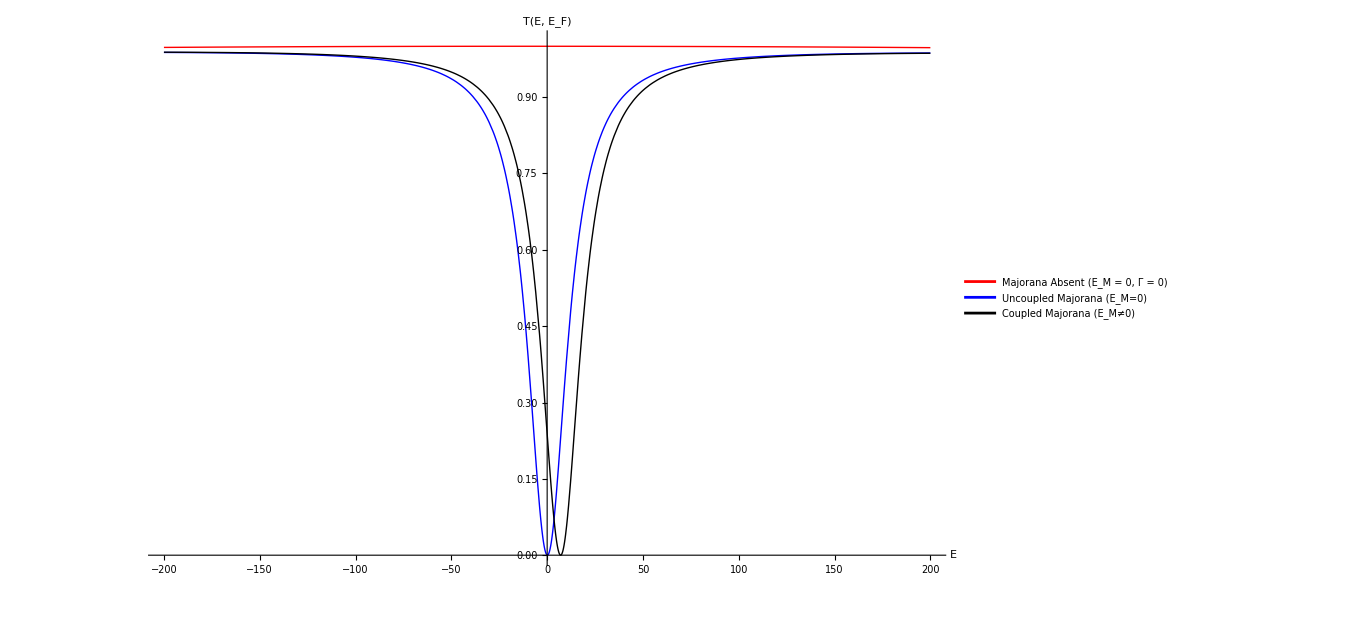

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;T2=Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57},(T1+T2)/.{Gf->10,GM->0,γ->51,ϕ->1.57},(T1+T2)/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-200,200},PlotRange->{0,1.01},PlotStyle->{{Red,Thick},{Blue,Thick},{Black, Thick}},AxesLabel->{Style["E",24,Black],Style["T(E, E_F)",24,Black]},PlotLegends->Placed[{Style["Majorana Absent (E_M = 0, Γ = 0)",24],Style["Uncoupled Majorana (E_M=0)",24],Style["Coupled Majorana (E_M≠0)",24]},{0.8,0.15}],AxesStyle->Directive[Gray,24],ImageSize->1000]
```

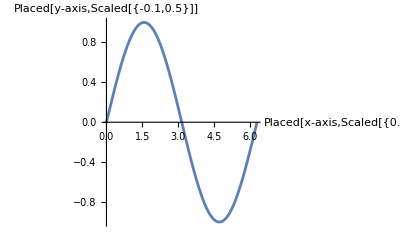

```mathematica
Plot[Sin[x],{x,0,2 Pi},AxesLabel->{Placed[Style["x-axis",14,Bold,Red],Scaled[{0.5,-0.1}]],Placed[Style["y-axis",14,Italic,Blue],Scaled[{-0.1,0.5}]]}]
```

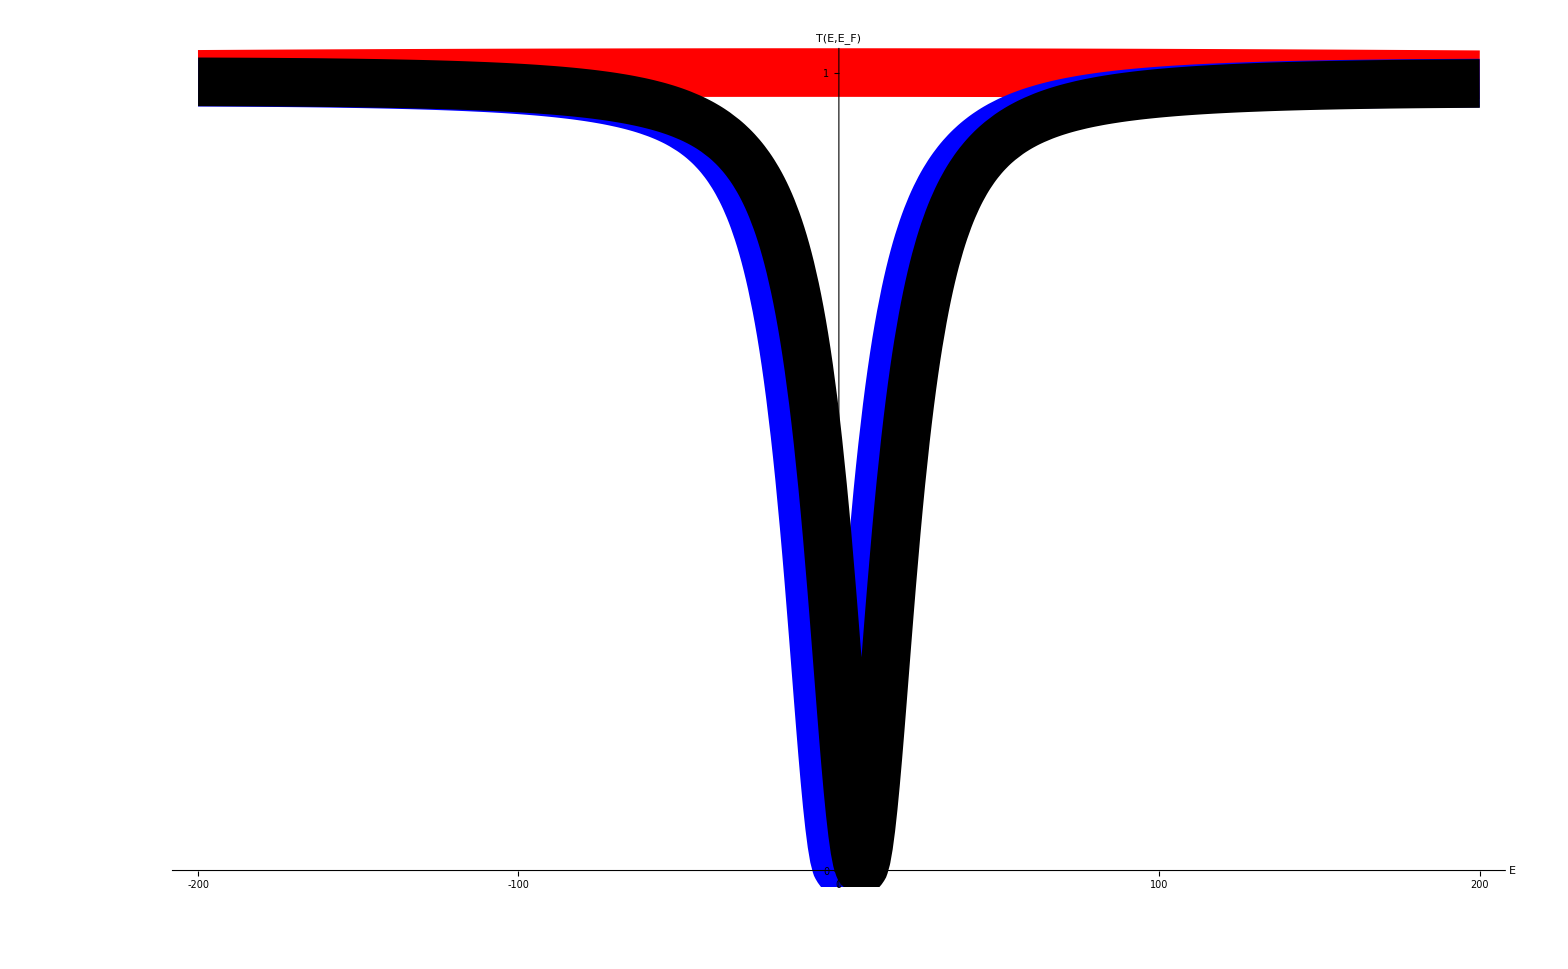

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;T2=Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
A8=Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57},(T1+T2)/.{Gf->10,GM->0,γ->51,ϕ->1.57},(T1+T2)/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0,1.01}},Ticks->{{-200,-100,0,100,200},{0,0.5,1}},PlotPoints->10,
AxesLabel->{Framed[Style["E",250,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->150],Framed[Style["T(E,E_F)",250,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->100]},TicksStyle->Directive[Black,150],PlotStyle->{Directive[AbsoluteThickness[35],Opacity[1],Red],Directive[AbsoluteThickness[35],Opacity[1],Blue],Directive[AbsoluteThickness[35],Opacity[1],Black]},ImageSize->5000,LabelStyle->Directive[Black,150]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->5000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[20]],Directive[Blue,AbsoluteThickness[20]],Directive[Black,AbsoluteThickness[20]]},{Style["Majorana Absent (E_M = 0, Γ = 0)",Black,150],Style["Uncoupled Majorana (E_M=0)",Black,150],Style["Coupled Majorana (E_M≠0)",Black,150]},LegendLayout->"Row",LegendMarkerSize->{400,200}],{0.999,0.20}]]
```

-Graphics-

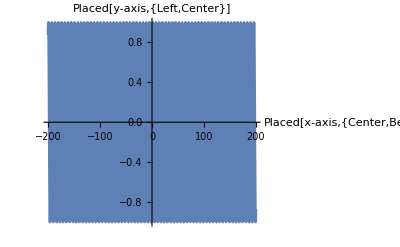

```mathematica
Plot[Sin[x],{x,-200,200},AxesLabel->{Placed[Style["x-axis",14,Bold],{Center,Below}],Placed[Style["y-axis",14,Bold],{Left,Center}]},LabelStyle->Directive[FontSize->14,Padding->{{5,5},{5,5}}],TicksStyle->Directive[FontSize->12]]
```

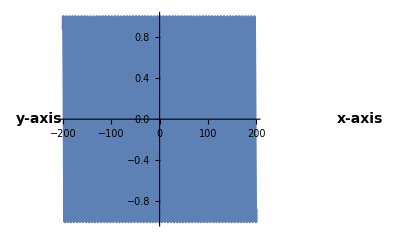

```mathematica
Plot[Sin[x],{x,-200,200},Axes->True,Ticks->Automatic,TicksStyle->Directive[FontSize->12],Epilog->{Text[Style["x-axis",14,Bold],Scaled[{1.5,0.5}]],Text[Style["y-axis",14,Bold],Scaled[{-0.1,0.5}]]},ImageSize->{400,300}]
```

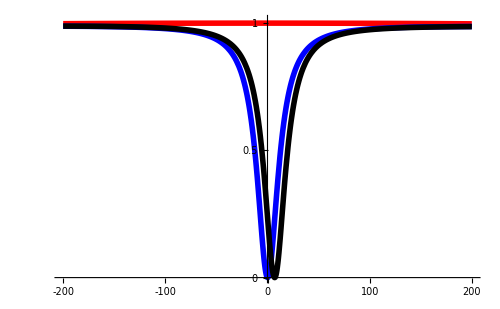
-Graphics-ET(E,E_F)

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;T2=Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
A8=Labeled[Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57},(T1+T2)/.{Gf->10,GM->0,γ->51,ϕ->1.57},(T1+T2)/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0,1.01}},Ticks->{{-200,-100,0,100,200},{0,0.5,1}},TicksStyle->Directive[Black,100],PlotStyle->{Directive[AbsoluteThickness[4],Opacity[1],Red],Directive[AbsoluteThickness[4],Opacity[1],Blue],Directive[AbsoluteThickness[4],Opacity[1],Black]},ImageSize->500,LabelStyle->Directive[Black,40]],{Style["E",50,Black],Style["T(E,E_F)",50,Black]},{Bottom,Top},RotateLabel->False]
```

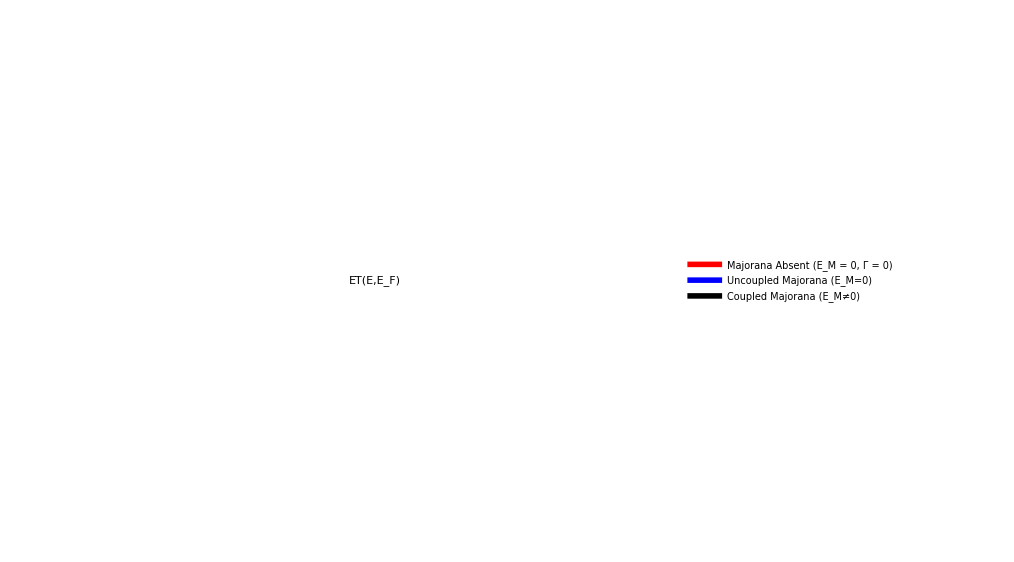

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->750],Placed[LineLegend[{Directive[Red,AbsoluteThickness[5]],Directive[Blue,AbsoluteThickness[5]],Directive[Black,AbsoluteThickness[5]]},{Style["Majorana Absent (E_M = 0, Γ = 0)",Black,10],Style["Uncoupled Majorana (E_M=0)",Black,10],Style["Coupled Majorana (E_M≠0)",Black,10]},LegendLayout->"Row",LegendMarkerSize->{50,20}],{0.85,0.40}]]
```

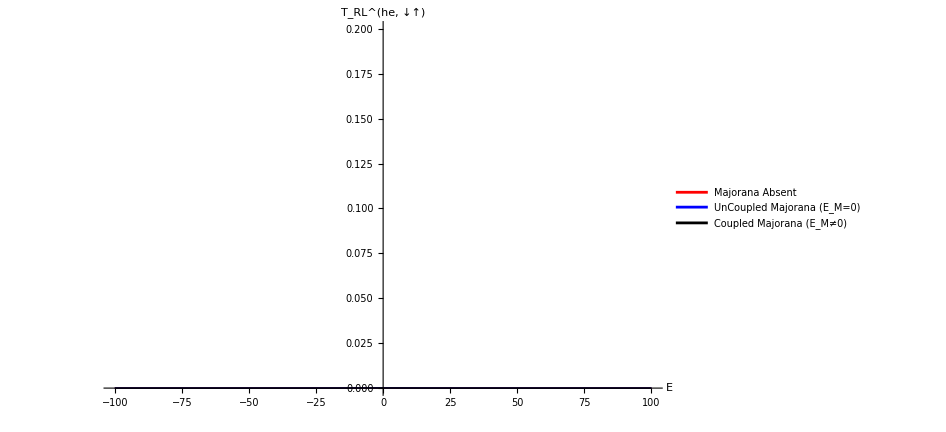

```mathematica
Plot[{T2/.{Gf->10,GM->0,γ->0,ϕ->1.57},T2/.{Gf->10,GM->0,γ->51,ϕ->1.57},T2/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-100,100},PlotRange->{0,0.2},PlotStyle->{{Red,Thick},{Blue,Thick},{Black, Thick}},AxesLabel->{Style["E",15,Bold,Black],Style["T_RL^(he, ↓↑)",15,Bold,Black]},PlotLegends->Placed[{Style["Majorana Absent",Bold,15],Style["UnCoupled Majorana (E_M=0)",Bold,15],Style["Coupled Majorana (E_M≠0)",Bold,15]},{Right,Top}],AxesStyle->Directive[Black,Bold, 15],ImageSize->700]
```

```mathematica
T2/.{}
```

```mathematica
(*a=1/2(√(1/2)-1);
b=1/2(√(1/2)+1);*)
l1=1/4;
l2=1/4;
ld=1/2;
L=1;
ke=(G+Gf)/(1000);
kh=(G-Gf)/(1000);
ke1=(G+Gf+Vg)/(1000);
kh1=(G-Gf-Vg)/(1000);
eo1u=1;
ho1d=0;
ei2u=0;
hi2d=0;
γ1=γ2=γ;
ϵ=0.5;
Vg=0;
Z= (GM  - G - I*γ )*(GM+G + I*γ );
x = γ*(G + I*γ )/Z;
x1 = γ*(G + I *γ)/Z;
y = GM*γ/Z;
P=Solve[{eiLu==(1+I x)*eoLu-y*eiRu+I x*hoLd-y*hiRd,
eoRu==y*eoLu+(1+I x1)*eiRu+y*hoLd+I x1*hiRd,
hiLd==I x*eoLu-y*eiRu+(1+I x)*hoLd-y*hiRd,
hoRd==y*eoLu+I x1*eiRu+y*hoLd+(1+I x1)*hiRd,

ei1u==-(a+b)*eo1u+p*eo3u+p*ei5u,
hi1d==-(a+b)ho1d+p*ho3d+p*hi5d,
ei3u==p*eo1u+a*eo3u+b*ei5u,
hi3d==p*ho1d+a*ho3d+b*hi5d,
eo5u==p*eo1u+b*eo3u+a*ei5u,
ho5d==p*ho1d+b*ho3d+a*hi5d,

eo2u==-(a+b)ei2u+p*ei4u+p*eo6u,
ho2d==-(a+b)hi2d+p*hi4d+p*ho6d,
eo4u==p*ei2u+a*ei4u+b*eo6u,
ho4d==p*hi2d+a*hi4d+b*ho6d,
ei6u==p*ei2u+b*ei4u+a*eo6u,
hi6d==p*hi2d+b*hi4d+a*ho6d,

ei5u==Exp[I*ke*l1]*Exp[-I*ϕ*l1]eiLu,
eoLu==Exp[I*ke*l1]*Exp[I*ϕ*l1]eo5u,
hi5d==Exp[I*kh*l1]*Exp[I*ϕ*l1]hiLd,
hoLd==Exp[I*kh*l1]*Exp[-I*ϕ*l1]ho5d,
eo6u==Exp[I*ke*l2]*Exp[I*ϕ*l2]eoRu,
eiRu==Exp[I*ke*l2]*Exp[-I*ϕ*l2]ei6u,
ho6d==Exp[I*kh*l2]*Exp[-I*ϕ*l2]hoRd,
hiRd==Exp[I*kh*l2]*Exp[I*ϕ*l2]hi6d,
eo3u==Exp[I*ke1*ld]*Exp[I*ϕ*ld]eo4u,
ei4u==Exp[I*ke1*ld]*Exp[-I*ϕ*ld]ei3u,
ho3d==Exp[I*kh1*ld]*Exp[-I*ϕ*ld]ho4d,
hi4d==Exp[I*kh1*ld]*Exp[I*ϕ*ld]hi3d}

,{eiLu,eoLu,eiRu,hoLd,hiRd,eoRu,hiLd,hoRd,ei1u,eo3u,ei5u,hi1d,ho3d,hi5d,ei3u,hi3d,eo5u,ho5d,eo2u,ei4u,eo6u,ho2d,hi4d,ho6d,eo4u,ho4d,ei6u,hi6d}];
ei1u=ei1u/.P[[1]];
hi1d=hi1d/.P[[1]];
eo2u=eo2u/.P[[1]]
ho2d=ho2d/.P[[1]]
```

```mathematica
eo2u//Simplify
```

(ⅇ^((ⅈ (G+Gf+1000 ϕ))/2000) p^2 (-2 b^3 ⅇ^((3 ⅈ (G+Gf))/2000) (-1+ⅇ^(2 ⅈ ϕ)) GM γ-2 b^5 ⅇ^((ⅈ (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-ⅈ G γ)+2 b ⅇ^((ⅈ (G+5 (Gf+400 ϕ)))/2000) (G^2-GM^2+ⅈ G γ)-a^6 ⅇ^((ⅈ (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 ⅈ G γ+ⅇ^(ⅈ ϕ) GM γ-γ^2)-b^6 ⅇ^((ⅈ (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 ⅈ G γ+ⅇ^(ⅈ ϕ) GM γ-γ^2)-ⅇ^((ⅈ Gf)/500+ⅈ ϕ) (-G^2+GM^2-2 ⅈ G γ+ⅇ^(ⅈ ϕ) GM γ+γ^2)+2 a^5 ⅇ^((ⅈ (5 G+Gf+2000 ϕ))/2000) ((1+ⅇ^((ⅈ Gf)/1000)+b ⅇ^((ⅈ (G+Gf))/2000)) G^2-(1+ⅇ^((ⅈ Gf)/1000)+b ⅇ^((ⅈ (G+Gf))/2000)) GM^2-ⅈ (1+ⅇ^((ⅈ Gf)/1000)+2 b ⅇ^((ⅈ (G+Gf))/2000)) G γ+ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) (b ⅇ^((ⅈ G)/2000)+ⅇ^((ⅈ Gf)/2000)) GM γ-b ⅇ^((ⅈ (G+Gf))/2000) γ^2)+b^4 ⅇ^((ⅈ G)/500) (ⅇ^(ⅈ ϕ) (-G^2+GM^2)+ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ+ⅇ^(2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+3 ⅈ ϕ) γ^2)+b^2 ⅇ^((ⅈ (G+Gf))/1000) (ⅇ^((ⅈ Gf)/500+ⅈ ϕ) (G^2-GM^2)+GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ-ⅇ^(2 ⅈ ϕ) GM γ-ⅇ^(3 ⅈ ϕ) γ^2)+a^4 ⅇ^((ⅈ G)/500+ⅈ ϕ) (-((1+4 ⅇ^((ⅈ Gf)/1000)-b^2 ⅇ^((ⅈ (G+Gf))/1000)+2 b ⅇ^((ⅈ (G+Gf))/2000) (1+2 ⅇ^((ⅈ Gf)/1000))) G^2)+(1+4 ⅇ^((ⅈ Gf)/1000)-b^2 ⅇ^((ⅈ (G+Gf))/1000)+2 b ⅇ^((ⅈ (G+Gf))/2000) (1+2 ⅇ^((ⅈ Gf)/1000))) GM^2-2 ⅈ ⅇ^((ⅈ Gf)/2000) (ⅇ^((3 ⅈ Gf)/2000)+b^2 ⅇ^((ⅈ (2 G+Gf))/2000)-b ⅇ^((ⅈ G)/2000) (1+2 ⅇ^((ⅈ Gf)/1000))) G γ-ⅇ^(ⅈ ϕ) (-1-b^2 ⅇ^((ⅈ (G+Gf))/1000)+4 b ⅇ^((ⅈ (G+3 Gf))/2000)) GM γ-ⅇ^((ⅈ Gf)/1000) (2+b^2 ⅇ^((ⅈ G)/1000)+ⅇ^((ⅈ Gf)/1000)) γ^2)+2 a^3 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) (-((-1+2 b^2 ⅇ^((ⅈ G)/1000)+ⅇ^((ⅈ Gf)/500)-2 b ⅇ^((ⅈ (G+Gf))/2000)+2 b^3 ⅇ^((ⅈ (3 G+Gf))/2000)) G^2)+(-1+2 b^2 ⅇ^((ⅈ G)/1000)+ⅇ^((ⅈ Gf)/500)-2 b ⅇ^((ⅈ (G+Gf))/2000)+2 b^3 ⅇ^((ⅈ (3 G+Gf))/2000)) GM^2+ⅈ (2 b^2 ⅇ^((ⅈ G)/1000)+4 b^3 ⅇ^((ⅈ (3 G+Gf))/2000)+2 b ⅇ^((ⅈ (G+3 Gf))/2000)+(1+ⅇ^((ⅈ Gf)/1000))^2) G γ-ⅇ^(ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/500)+2 b^3 ⅇ^((ⅈ (3 G+Gf))/2000)) GM γ+b ⅇ^((ⅈ (G+Gf))/2000) (1+2 b^2 ⅇ^((ⅈ G)/1000)+ⅇ^((ⅈ Gf)/1000)) γ^2)+a^2 ⅇ^((ⅈ G)/1000) (b^4 ⅇ^((ⅈ (2 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 ⅈ G γ+ⅇ^(ⅈ ϕ) GM γ-γ^2)+4 b^3 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) ((1+ⅇ^((ⅈ Gf)/1000)) G^2-ⅈ (1+ⅇ^((ⅈ Gf)/1000)) G γ-GM (GM+ⅇ^((ⅈ Gf)/1000) GM-ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) γ))+4 b ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) (-ⅈ G γ+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/1000) (G^2-GM^2-ⅈ G γ))+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (ⅇ^((ⅈ Gf)/500) (G^2-GM^2)+ⅇ^((ⅈ Gf)/500+ⅈ ϕ) GM γ+γ (-2 ⅈ G+γ)+2 ⅇ^((ⅈ Gf)/1000) (2 G^2-2 GM^2+γ^2))+b^2 ⅇ^((ⅈ G)/1000) (2 ⅇ^(ⅈ ϕ) (G^2-GM^2)+ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ-2 ⅇ^(2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+ⅈ ϕ) (-2 ⅈ G-γ) γ+ⅇ^((ⅈ Gf)/500+3 ⅈ ϕ) γ^2+2 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (2 G^2-2 GM^2+γ^2)))-2 a ⅇ^((ⅈ (G+Gf))/2000) (-b^5 ⅇ^((ⅈ (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-2 ⅈ G γ+ⅇ^(ⅈ ϕ) GM γ-γ^2)+b ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) ((2+ⅇ^((ⅈ Gf)/1000)) G^2-(2+ⅇ^((ⅈ Gf)/1000)) GM^2+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM γ+γ^2)+b^4 ⅇ^((ⅈ G)/500+ⅈ ϕ) ((-1+ⅇ^((ⅈ Gf)/1000)) G^2-ⅈ (-1+ⅇ^((ⅈ Gf)/1000)) G γ+GM (GM-ⅇ^((ⅈ Gf)/1000) GM+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) γ))+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) ((1+ⅇ^((ⅈ Gf)/1000)) G^2+ⅈ (1+ⅇ^((ⅈ Gf)/1000)) G γ-GM (GM+ⅇ^((ⅈ Gf)/1000) GM+ⅇ^(ⅈ ϕ) γ))+b^2 ⅇ^((ⅈ G)/1000) (ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ-ⅇ^(2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+ⅈ ϕ) (G^2-GM^2-ⅈ G γ)+ⅇ^(ⅈ ϕ) (G^2-GM^2+ⅈ G γ))+b^3 ⅇ^((ⅈ (3 G+Gf))/2000) (ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/1000+3 ⅈ ϕ) γ^2+ⅇ^(ⅈ ϕ) (2 G^2-2 GM^2+γ^2)))))/(b^2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) (-1+ⅇ^((ⅈ Gf)/500)) (-1+ⅇ^(2 ⅈ ϕ)) GM γ+b^6 ⅇ^((ⅈ (3 G+Gf+1000 ϕ))/1000) (-1+ⅇ^((ⅈ Gf)/500)) (-1+ⅇ^(2 ⅈ ϕ)) GM γ-2 a^7 ⅇ^((ⅈ (7 G+3 Gf+4000 ϕ))/2000) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2-ⅈ G γ)+2 a^5 ⅇ^((ⅈ (5 G+Gf+4000 ϕ))/2000) (1+ⅇ^((ⅈ Gf)/1000)) ((1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)+3 b^2 ⅇ^((ⅈ (G+Gf))/1000)) G^2-(1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)+3 b^2 ⅇ^((ⅈ (G+Gf))/1000)) GM^2-ⅈ (1+ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)+3 b^2 ⅇ^((ⅈ (G+Gf))/1000)) G γ)+a^8 ⅇ^(1/500 ⅈ (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 ⅈ G γ-γ^2)+b^8 ⅇ^(1/500 ⅈ (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 ⅈ G γ-γ^2)+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+b^4 ⅇ^((ⅈ G)/500) (ⅇ^((ⅈ Gf)/250+2 ⅈ ϕ) (-G^2+GM^2)+ⅇ^(2 ⅈ ϕ) (-G^2+GM^2)+ⅇ^((ⅈ Gf)/500) γ^2+ⅇ^((ⅈ Gf)/500+4 ⅈ ϕ) γ^2)+a^6 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/1000) (γ (2 ⅈ G+γ)+ⅇ^((ⅈ Gf)/500) γ (2 ⅈ G+γ)-4 b^2 ⅇ^((ⅈ (G+Gf))/1000) (G^2-GM^2-2 ⅈ G γ-γ^2)+2 ⅇ^((ⅈ Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 ⅇ^((ⅈ G)/500+ⅈ ϕ) (ⅇ^((ⅈ Gf)/250+ⅈ ϕ) (-G^2+GM^2)+ⅇ^(ⅈ ϕ) (-G^2+GM^2)+b^2 ⅇ^((ⅈ (G+Gf))/1000) GM γ-b^2 ⅇ^((ⅈ (G+3 Gf))/1000) GM γ-b^2 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) GM γ+b^2 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/1000) GM γ-2 ⅈ b^2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) (2 G-ⅈ γ) γ-2 ⅈ b^2 ⅇ^((ⅈ (G+3 Gf+1000 ϕ))/1000) (2 G-ⅈ γ) γ-2 ⅇ^((ⅈ Gf)/500+ⅈ ϕ) γ^2+6 b^4 ⅇ^(1/500 ⅈ (G+Gf+500 ϕ)) (G^2-GM^2-2 ⅈ G γ-γ^2)-2 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (2 G^2-2 GM^2+γ^2)-2 ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) (-3 b^4 ⅇ^((ⅈ (2 G+Gf+1000 ϕ))/1000) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2-ⅈ G γ)+ⅇ^(ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/1000)) ((1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) G^2-(1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) GM^2+ⅈ (1+ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) G γ)-b^2 ⅇ^((ⅈ G)/1000) (-2 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G γ-2 ⅈ ⅇ^((ⅈ Gf)/500+ⅈ ϕ) G γ+ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ+2 ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2-ⅈ G γ)+2 ⅇ^(ⅈ ϕ) (G^2-GM^2-ⅈ G γ)))+2 a ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) (b^6 ⅇ^((ⅈ (3 G+Gf+1000 ϕ))/1000) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2-ⅈ G γ)-ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2+ⅈ G γ)+b^4 ⅇ^((ⅈ G)/500) (ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ+ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2-ⅈ G γ)+ⅇ^(ⅈ ϕ) (G^2-GM^2-ⅈ G γ))-b^2 ⅇ^((ⅈ G)/1000) (ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ+ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2+ⅈ G γ)+ⅇ^(ⅈ ϕ) (G^2-GM^2+ⅈ G γ)))+a^2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) (-4 b^6 ⅇ^((ⅈ (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 ⅈ G γ-γ^2)+2 b^2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) ((1+2 ⅇ^((ⅈ Gf)/1000)+2 ⅇ^((3 ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/250)) G^2-(1+2 ⅇ^((ⅈ Gf)/1000)+2 ⅇ^((3 ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/250)) GM^2+ⅇ^((ⅈ Gf)/1000) (1+ⅇ^((ⅈ Gf)/500)) γ^2)+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (γ (-2 ⅈ G+γ)+ⅇ^((ⅈ Gf)/500) γ (-2 ⅈ G+γ)+2 ⅇ^((ⅈ Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 ⅇ^((ⅈ (2 G+Gf))/1000) (2 GM γ-2 ⅇ^((ⅈ Gf)/500) GM γ+2 ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ-2 ⅇ^(2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+ⅈ ϕ) (-2 ⅈ G-γ) γ+ⅇ^(ⅈ ϕ) (-2 ⅈ G-γ) γ-2 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (2 G^2-2 GM^2+γ^2))))

```mathematica
ho2d//Simplify
```

-((ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) p^2 γ (ⅇ^((3 ⅈ Gf)/2000+ⅈ ϕ) GM+a^6 ⅇ^((ⅈ (6 G+3 Gf+2000 ϕ))/2000) GM+b^6 ⅇ^((ⅈ (6 G+3 Gf+2000 ϕ))/2000) GM+b^3 ⅇ^((3 ⅈ G)/2000+ⅈ ϕ) (-1+ⅇ^((ⅈ Gf)/1000))^2 (1+ⅇ^((ⅈ Gf)/1000)) GM-a^5 ⅇ^((ⅈ (5 G+2 Gf+2000 ϕ))/2000) (1+ⅇ^((ⅈ Gf)/1000)+2 b ⅇ^((ⅈ (G+Gf))/2000)) GM+ⅈ b^4 ⅇ^((ⅈ (4 G+Gf))/2000) (G+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) G+ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM)+ⅈ b^2 ⅇ^((ⅈ (2 G+Gf))/2000) (ⅇ^((ⅈ Gf)/500) G+ⅇ^(2 ⅈ ϕ) G+ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM)-a^2 ⅇ^((ⅈ G)/1000) (b^4 ⅇ^((ⅈ (4 G+3 Gf+2000 ϕ))/2000) GM+2 b^3 ⅇ^((ⅈ (3 G+2 Gf+2000 ϕ))/2000) (1+ⅇ^((ⅈ Gf)/1000)) GM+ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) (1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) GM+ⅈ b^2 ⅇ^((ⅈ (2 G+Gf))/2000) ((1+2 ⅇ^((ⅈ Gf)/1000)+2 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ)+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ)) G+ⅈ ⅇ^(ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/500)) GM)+b ⅇ^((ⅈ G)/2000) (ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM+ⅇ^((ⅈ Gf)/500+ⅈ ϕ) GM+ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) GM+ⅇ^(ⅈ ϕ) GM+ⅇ^((ⅈ Gf)/500) (-ⅈ G-γ)+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (-ⅈ G-γ)+ⅈ ⅇ^((ⅈ Gf)/1000) (G+ⅈ γ)+ⅈ ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) (G+ⅈ γ)))+ⅈ b ⅇ^((ⅈ (G+2 Gf))/2000) (ⅇ^((ⅈ Gf)/1000)+ⅇ^(2 ⅈ ϕ)) (G+ⅈ γ)+b^5 ⅇ^((ⅈ (5 G+2 Gf))/2000) (1+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ)) (ⅈ G+γ)+a^3 ⅇ^((3 ⅈ G)/2000) (4 b^3 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM+ⅇ^(ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)+ⅇ^((3 ⅈ Gf)/1000)) GM+b ⅇ^((ⅈ (G+Gf))/2000) (ⅈ (1+ⅇ^((ⅈ Gf)/1000)) (1+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ)) G+ⅇ^(ⅈ ϕ) (-1+ⅇ^((ⅈ Gf)/1000))^2 GM)+2 b^2 ⅇ^((ⅈ (G+Gf))/1000) (1+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ)) (ⅈ G+γ))-a^4 ⅇ^((ⅈ (4 G+Gf))/2000) (b^2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) GM+ⅇ^(ⅈ ϕ) (1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) GM+b ⅇ^((ⅈ (G+Gf))/2000) (ⅈ (1+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ)) G-2 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM-2 ⅇ^(ⅈ ϕ) GM+γ+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ))-a ⅇ^((ⅈ G)/2000) (2 b^5 ⅇ^((ⅈ (5 G+3 Gf+2000 ϕ))/2000) GM+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/1000)) GM+ⅈ b ⅇ^((ⅈ (G+Gf))/2000) (ⅇ^((ⅈ Gf)/1000) G+ⅇ^((ⅈ Gf)/500) G+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G+ⅇ^(2 ⅈ ϕ) G+ⅈ ⅇ^((ⅈ Gf)/500+ⅈ ϕ) GM+ⅈ ⅇ^(ⅈ ϕ) GM)+b^3 ⅇ^((ⅈ (3 G+Gf))/2000) (-1+ⅇ^((ⅈ Gf)/1000)) (ⅈ (-1+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ)) G+ⅇ^(ⅈ ϕ) (-1+ⅇ^((ⅈ Gf)/1000)) GM)+b^4 ⅇ^((ⅈ (2 G+Gf))/1000) (2 ⅈ (1+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ)) G-ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM-ⅇ^(ⅈ ϕ) GM+2 γ+2 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ)+b^2 ⅇ^((ⅈ G)/1000) (-ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM-ⅇ^((ⅈ Gf)/500+ⅈ ϕ) GM+ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) GM+ⅇ^(ⅈ ϕ) GM+ⅇ^((ⅈ Gf)/1000) (-ⅈ G+γ)+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) (-ⅈ G+γ)+ⅇ^((ⅈ Gf)/500) (ⅈ G+γ)+ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (ⅈ G+γ)))))/(b^2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) (-1+ⅇ^((ⅈ Gf)/500)) (-1+ⅇ^(2 ⅈ ϕ)) GM γ+b^6 ⅇ^((ⅈ (3 G+Gf+1000 ϕ))/1000) (-1+ⅇ^((ⅈ Gf)/500)) (-1+ⅇ^(2 ⅈ ϕ)) GM γ-2 a^7 ⅇ^((ⅈ (7 G+3 Gf+4000 ϕ))/2000) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2-ⅈ G γ)+2 a^5 ⅇ^((ⅈ (5 G+Gf+4000 ϕ))/2000) (1+ⅇ^((ⅈ Gf)/1000)) ((1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)+3 b^2 ⅇ^((ⅈ (G+Gf))/1000)) G^2-(1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)+3 b^2 ⅇ^((ⅈ (G+Gf))/1000)) GM^2-ⅈ (1+ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)+3 b^2 ⅇ^((ⅈ (G+Gf))/1000)) G γ)+a^8 ⅇ^(1/500 ⅈ (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 ⅈ G γ-γ^2)+b^8 ⅇ^(1/500 ⅈ (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 ⅈ G γ-γ^2)+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+b^4 ⅇ^((ⅈ G)/500) (ⅇ^((ⅈ Gf)/250+2 ⅈ ϕ) (-G^2+GM^2)+ⅇ^(2 ⅈ ϕ) (-G^2+GM^2)+ⅇ^((ⅈ Gf)/500) γ^2+ⅇ^((ⅈ Gf)/500+4 ⅈ ϕ) γ^2)+a^6 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/1000) (γ (2 ⅈ G+γ)+ⅇ^((ⅈ Gf)/500) γ (2 ⅈ G+γ)-4 b^2 ⅇ^((ⅈ (G+Gf))/1000) (G^2-GM^2-2 ⅈ G γ-γ^2)+2 ⅇ^((ⅈ Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 ⅇ^((ⅈ G)/500+ⅈ ϕ) (ⅇ^((ⅈ Gf)/250+ⅈ ϕ) (-G^2+GM^2)+ⅇ^(ⅈ ϕ) (-G^2+GM^2)+b^2 ⅇ^((ⅈ (G+Gf))/1000) GM γ-b^2 ⅇ^((ⅈ (G+3 Gf))/1000) GM γ-b^2 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) GM γ+b^2 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/1000) GM γ-2 ⅈ b^2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) (2 G-ⅈ γ) γ-2 ⅈ b^2 ⅇ^((ⅈ (G+3 Gf+1000 ϕ))/1000) (2 G-ⅈ γ) γ-2 ⅇ^((ⅈ Gf)/500+ⅈ ϕ) γ^2+6 b^4 ⅇ^(1/500 ⅈ (G+Gf+500 ϕ)) (G^2-GM^2-2 ⅈ G γ-γ^2)-2 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (2 G^2-2 GM^2+γ^2)-2 ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) (-3 b^4 ⅇ^((ⅈ (2 G+Gf+1000 ϕ))/1000) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2-ⅈ G γ)+ⅇ^(ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/1000)) ((1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) G^2-(1-ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) GM^2+ⅈ (1+ⅇ^((ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/500)) G γ)-b^2 ⅇ^((ⅈ G)/1000) (-2 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G γ-2 ⅈ ⅇ^((ⅈ Gf)/500+ⅈ ϕ) G γ+ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ+2 ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2-ⅈ G γ)+2 ⅇ^(ⅈ ϕ) (G^2-GM^2-ⅈ G γ)))+2 a ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) (b^6 ⅇ^((ⅈ (3 G+Gf+1000 ϕ))/1000) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2-ⅈ G γ)-ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (1+ⅇ^((ⅈ Gf)/1000)) (G^2-GM^2+ⅈ G γ)+b^4 ⅇ^((ⅈ G)/500) (ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ+ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2-ⅈ G γ)+ⅇ^(ⅈ ϕ) (G^2-GM^2-ⅈ G γ))-b^2 ⅇ^((ⅈ G)/1000) (ⅇ^((ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ Gf)/500) GM γ-ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ+ⅇ^((3 ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2+ⅈ G γ)+ⅇ^(ⅈ ϕ) (G^2-GM^2+ⅈ G γ)))+a^2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) (-4 b^6 ⅇ^((ⅈ (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 ⅈ G γ-γ^2)+2 b^2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) ((1+2 ⅇ^((ⅈ Gf)/1000)+2 ⅇ^((3 ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/250)) G^2-(1+2 ⅇ^((ⅈ Gf)/1000)+2 ⅇ^((3 ⅈ Gf)/1000)+ⅇ^((ⅈ Gf)/250)) GM^2+ⅇ^((ⅈ Gf)/1000) (1+ⅇ^((ⅈ Gf)/500)) γ^2)+ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (γ (-2 ⅈ G+γ)+ⅇ^((ⅈ Gf)/500) γ (-2 ⅈ G+γ)+2 ⅇ^((ⅈ Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 ⅇ^((ⅈ (2 G+Gf))/1000) (2 GM γ-2 ⅇ^((ⅈ Gf)/500) GM γ+2 ⅇ^((ⅈ Gf)/500+2 ⅈ ϕ) GM γ-2 ⅇ^(2 ⅈ ϕ) GM γ+ⅇ^((ⅈ Gf)/500+ⅈ ϕ) (-2 ⅈ G-γ) γ+ⅇ^(ⅈ ϕ) (-2 ⅈ G-γ) γ-2 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (2 G^2-2 GM^2+γ^2)))))

```mathematica
eo2u=(E^((I (G+Gf+1000 ϕ))/2000) p^2 (-2 b^3 E^((3 I (G+Gf))/2000) (-1+E^(2 I ϕ)) GM γ-2 b^5 E^((I (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+2 b E^((I (G+5 (Gf+400 ϕ)))/2000) (G^2-GM^2+I G γ)-a^6 E^((I (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)-b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)-E^((I Gf)/500+I ϕ) (-G^2+GM^2-2 I G γ+E^(I ϕ) GM γ+γ^2)+2 a^5 E^((I (5 G+Gf+2000 ϕ))/2000) ((1+E^((I Gf)/1000)+b E^((I (G+Gf))/2000)) G^2-(1+E^((I Gf)/1000)+b E^((I (G+Gf))/2000)) GM^2-I (1+E^((I Gf)/1000)+2 b E^((I (G+Gf))/2000)) G γ+E^((I Gf)/2000+I ϕ) (b E^((I G)/2000)+E^((I Gf)/2000)) GM γ-b E^((I (G+Gf))/2000) γ^2)+b^4 E^((I G)/500) (E^(I ϕ) (-G^2+GM^2)+E^((I Gf)/500) GM γ-E^((I Gf)/500+2 I ϕ) GM γ+E^(2 I ϕ) GM γ+E^((I Gf)/500+3 I ϕ) γ^2)+b^2 E^((I (G+Gf))/1000) (E^((I Gf)/500+I ϕ) (G^2-GM^2)+GM γ+E^((I Gf)/500+2 I ϕ) GM γ-E^(2 I ϕ) GM γ-E^(3 I ϕ) γ^2)+a^4 E^((I G)/500+I ϕ) (-((1+4 E^((I Gf)/1000)-b^2 E^((I (G+Gf))/1000)+2 b E^((I (G+Gf))/2000) (1+2 E^((I Gf)/1000))) G^2)+(1+4 E^((I Gf)/1000)-b^2 E^((I (G+Gf))/1000)+2 b E^((I (G+Gf))/2000) (1+2 E^((I Gf)/1000))) GM^2-2 I E^((I Gf)/2000) (E^((3 I Gf)/2000)+b^2 E^((I (2 G+Gf))/2000)-b E^((I G)/2000) (1+2 E^((I Gf)/1000))) G γ-E^(I ϕ) (-1-b^2 E^((I (G+Gf))/1000)+4 b E^((I (G+3 Gf))/2000)) GM γ-E^((I Gf)/1000) (2+b^2 E^((I G)/1000)+E^((I Gf)/1000)) γ^2)+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-((-1+2 b^2 E^((I G)/1000)+E^((I Gf)/500)-2 b E^((I (G+Gf))/2000)+2 b^3 E^((I (3 G+Gf))/2000)) G^2)+(-1+2 b^2 E^((I G)/1000)+E^((I Gf)/500)-2 b E^((I (G+Gf))/2000)+2 b^3 E^((I (3 G+Gf))/2000)) GM^2+I (2 b^2 E^((I G)/1000)+4 b^3 E^((I (3 G+Gf))/2000)+2 b E^((I (G+3 Gf))/2000)+(1+E^((I Gf)/1000))^2) G γ-E^(I ϕ) (1+E^((I Gf)/500)+2 b^3 E^((I (3 G+Gf))/2000)) GM γ+b E^((I (G+Gf))/2000) (1+2 b^2 E^((I G)/1000)+E^((I Gf)/1000)) γ^2)+a^2 E^((I G)/1000) (b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)+4 b^3 E^((I (3 G+Gf+2000 ϕ))/2000) ((1+E^((I Gf)/1000)) G^2-I (1+E^((I Gf)/1000)) G γ-GM (GM+E^((I Gf)/1000) GM-E^((I Gf)/1000+I ϕ) γ))+4 b E^((I (G+3 Gf+2000 ϕ))/2000) (-I G γ+E^((I Gf)/1000+I ϕ) GM γ+E^((I Gf)/1000) (G^2-GM^2-I G γ))+E^((I Gf)/1000+I ϕ) (E^((I Gf)/500) (G^2-GM^2)+E^((I Gf)/500+I ϕ) GM γ+γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+b^2 E^((I G)/1000) (2 E^(I ϕ) (G^2-GM^2)+E^((I Gf)/500) GM γ-E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^((I Gf)/500+3 I ϕ) γ^2+2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)))-2 a E^((I (G+Gf))/2000) (-b^5 E^((I (5 G+Gf+2000 ϕ))/2000) (G^2-GM^2-2 I G γ+E^(I ϕ) GM γ-γ^2)+b E^((I (G+3 Gf+2000 ϕ))/2000) ((2+E^((I Gf)/1000)) G^2-(2+E^((I Gf)/1000)) GM^2+E^((I Gf)/1000+I ϕ) GM γ+γ^2)+b^4 E^((I G)/500+I ϕ) ((-1+E^((I Gf)/1000)) G^2-I (-1+E^((I Gf)/1000)) G γ+GM (GM-E^((I Gf)/1000) GM+E^((I Gf)/1000+I ϕ) γ))+E^((I Gf)/1000+I ϕ) ((1+E^((I Gf)/1000)) G^2+I (1+E^((I Gf)/1000)) G γ-GM (GM+E^((I Gf)/1000) GM+E^(I ϕ) γ))+b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ-E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2+I G γ))+b^3 E^((I (3 G+Gf))/2000) (E^((I Gf)/1000) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/1000+3 I ϕ) γ^2+E^(I ϕ) (2 G^2-2 GM^2+γ^2)))))/(b^2 E^((I (G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ+b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ-2 a^7 E^((I (7 G+3 Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+2 a^5 E^((I (5 G+Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) GM^2-I (1+E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G γ)+a^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+b^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+E^((I Gf)/500+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+b^4 E^((I G)/500) (E^((I Gf)/250+2 I ϕ) (-G^2+GM^2)+E^(2 I ϕ) (-G^2+GM^2)+E^((I Gf)/500) γ^2+E^((I Gf)/500+4 I ϕ) γ^2)+a^6 E^((I (3 G+Gf+2000 ϕ))/1000) (γ (2 I G+γ)+E^((I Gf)/500) γ (2 I G+γ)-4 b^2 E^((I (G+Gf))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 E^((I G)/500+I ϕ) (E^((I Gf)/250+I ϕ) (-G^2+GM^2)+E^(I ϕ) (-G^2+GM^2)+b^2 E^((I (G+Gf))/1000) GM γ-b^2 E^((I (G+3 Gf))/1000) GM γ-b^2 E^((I (G+Gf+2000 ϕ))/1000) GM γ+b^2 E^((I (G+3 Gf+2000 ϕ))/1000) GM γ-2 I b^2 E^((I (G+Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 I b^2 E^((I (G+3 Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 E^((I Gf)/500+I ϕ) γ^2+6 b^4 E^(1/500 I (G+Gf+500 ϕ)) (G^2-GM^2-2 I G γ-γ^2)-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-2 E^((3 I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 E^((I (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-3 b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+E^(I ϕ) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)) GM^2+I (1+E^((I Gf)/1000)+E^((I Gf)/500)) G γ)-b^2 E^((I G)/1000) (-2 I E^((I Gf)/1000+I ϕ) G γ-2 I E^((I Gf)/500+I ϕ) G γ+E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+2 E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+2 E^(I ϕ) (G^2-GM^2-I G γ)))+2 a E^((I (G+Gf+2000 ϕ))/2000) (b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)-E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) (G^2-GM^2+I G γ)+b^4 E^((I G)/500) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2-I G γ))-b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2+I G γ)+E^(I ϕ) (G^2-GM^2+I G γ)))+a^2 E^((I G)/1000+I ϕ) (-4 b^6 E^((I (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 b^2 E^((I G)/1000+I ϕ) ((1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) G^2-(1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) GM^2+E^((I Gf)/1000) (1+E^((I Gf)/500)) γ^2)+E^((I Gf)/1000+I ϕ) (γ (-2 I G+γ)+E^((I Gf)/500) γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 E^((I (2 G+Gf))/1000) (2 GM γ-2 E^((I Gf)/500) GM γ+2 E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^(I ϕ) (-2 I G-γ) γ-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2))));
ho2d=-((E^((I (G+Gf+2000 ϕ))/2000) p^2 γ (E^((3 I Gf)/2000+I ϕ) GM+a^6 E^((I (6 G+3 Gf+2000 ϕ))/2000) GM+b^6 E^((I (6 G+3 Gf+2000 ϕ))/2000) GM+b^3 E^((3 I G)/2000+I ϕ) (-1+E^((I Gf)/1000))^2 (1+E^((I Gf)/1000)) GM-a^5 E^((I (5 G+2 Gf+2000 ϕ))/2000) (1+E^((I Gf)/1000)+2 b E^((I (G+Gf))/2000)) GM+I b^4 E^((I (4 G+Gf))/2000) (G+E^((I Gf)/500+2 I ϕ) G+I E^((I Gf)/1000+I ϕ) GM)+I b^2 E^((I (2 G+Gf))/2000) (E^((I Gf)/500) G+E^(2 I ϕ) G+I E^((I Gf)/1000+I ϕ) GM)-a^2 E^((I G)/1000) (b^4 E^((I (4 G+3 Gf+2000 ϕ))/2000) GM+2 b^3 E^((I (3 G+2 Gf+2000 ϕ))/2000) (1+E^((I Gf)/1000)) GM+E^((I Gf)/2000+I ϕ) (1-E^((I Gf)/1000)+E^((I Gf)/500)) GM+I b^2 E^((I (2 G+Gf))/2000) ((1+2 E^((I Gf)/1000)+2 E^((I Gf)/1000+2 I ϕ)+E^((I Gf)/500+2 I ϕ)) G+I E^(I ϕ) (1+E^((I Gf)/500)) GM)+b E^((I G)/2000) (E^((I Gf)/1000+I ϕ) GM+E^((I Gf)/500+I ϕ) GM+E^((3 I Gf)/1000+I ϕ) GM+E^(I ϕ) GM+E^((I Gf)/500) (-I G-γ)+E^((I Gf)/1000+2 I ϕ) (-I G-γ)+I E^((I Gf)/1000) (G+I γ)+I E^((I Gf)/500+2 I ϕ) (G+I γ)))+I b E^((I (G+2 Gf))/2000) (E^((I Gf)/1000)+E^(2 I ϕ)) (G+I γ)+b^5 E^((I (5 G+2 Gf))/2000) (1+E^((I Gf)/1000+2 I ϕ)) (I G+γ)+a^3 E^((3 I G)/2000) (4 b^3 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+E^(I ϕ) (1+E^((I Gf)/1000)+E^((I Gf)/500)+E^((3 I Gf)/1000)) GM+b E^((I (G+Gf))/2000) (I (1+E^((I Gf)/1000)) (1+E^((I Gf)/1000+2 I ϕ)) G+E^(I ϕ) (-1+E^((I Gf)/1000))^2 GM)+2 b^2 E^((I (G+Gf))/1000) (1+E^((I Gf)/1000+2 I ϕ)) (I G+γ))-a^4 E^((I (4 G+Gf))/2000) (b^2 E^((I (G+Gf+1000 ϕ))/1000) GM+E^(I ϕ) (1-E^((I Gf)/1000)+E^((I Gf)/500)) GM+b E^((I (G+Gf))/2000) (I (1+E^((I Gf)/1000+2 I ϕ)) G-2 E^((I Gf)/1000+I ϕ) GM-2 E^(I ϕ) GM+γ+E^((I Gf)/1000+2 I ϕ) γ))-a E^((I G)/2000) (2 b^5 E^((I (5 G+3 Gf+2000 ϕ))/2000) GM+E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) GM+I b E^((I (G+Gf))/2000) (E^((I Gf)/1000) G+E^((I Gf)/500) G+E^((I Gf)/1000+2 I ϕ) G+E^(2 I ϕ) G+I E^((I Gf)/500+I ϕ) GM+I E^(I ϕ) GM)+b^3 E^((I (3 G+Gf))/2000) (-1+E^((I Gf)/1000)) (I (-1+E^((I Gf)/1000+2 I ϕ)) G+E^(I ϕ) (-1+E^((I Gf)/1000)) GM)+b^4 E^((I (2 G+Gf))/1000) (2 I (1+E^((I Gf)/1000+2 I ϕ)) G-E^((I Gf)/1000+I ϕ) GM-E^(I ϕ) GM+2 γ+2 E^((I Gf)/1000+2 I ϕ) γ)+b^2 E^((I G)/1000) (-E^((I Gf)/1000+I ϕ) GM-E^((I Gf)/500+I ϕ) GM+E^((3 I Gf)/1000+I ϕ) GM+E^(I ϕ) GM+E^((I Gf)/1000) (-I G+γ)+E^((I Gf)/500+2 I ϕ) (-I G+γ)+E^((I Gf)/500) (I G+γ)+E^((I Gf)/1000+2 I ϕ) (I G+γ)))))/(b^2 E^((I (G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ+b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (-1+E^((I Gf)/500)) (-1+E^(2 I ϕ)) GM γ-2 a^7 E^((I (7 G+3 Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+2 a^5 E^((I (5 G+Gf+4000 ϕ))/2000) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) GM^2-I (1+E^((I Gf)/1000)+E^((I Gf)/500)+3 b^2 E^((I (G+Gf))/1000)) G γ)+a^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+b^8 E^(1/500 I (2 G+Gf+1000 ϕ)) (G^2-GM^2-2 I G γ-γ^2)+E^((I Gf)/500+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+b^4 E^((I G)/500) (E^((I Gf)/250+2 I ϕ) (-G^2+GM^2)+E^(2 I ϕ) (-G^2+GM^2)+E^((I Gf)/500) γ^2+E^((I Gf)/500+4 I ϕ) γ^2)+a^6 E^((I (3 G+Gf+2000 ϕ))/1000) (γ (2 I G+γ)+E^((I Gf)/500) γ (2 I G+γ)-4 b^2 E^((I (G+Gf))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))+a^4 E^((I G)/500+I ϕ) (E^((I Gf)/250+I ϕ) (-G^2+GM^2)+E^(I ϕ) (-G^2+GM^2)+b^2 E^((I (G+Gf))/1000) GM γ-b^2 E^((I (G+3 Gf))/1000) GM γ-b^2 E^((I (G+Gf+2000 ϕ))/1000) GM γ+b^2 E^((I (G+3 Gf+2000 ϕ))/1000) GM γ-2 I b^2 E^((I (G+Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 I b^2 E^((I (G+3 Gf+1000 ϕ))/1000) (2 G-I γ) γ-2 E^((I Gf)/500+I ϕ) γ^2+6 b^4 E^(1/500 I (G+Gf+500 ϕ)) (G^2-GM^2-2 I G γ-γ^2)-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-2 E^((3 I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)-4 b^2 E^((I (G+2 (Gf+500 ϕ)))/1000) (2 G^2-2 GM^2+γ^2))+2 a^3 E^((I (3 G+Gf+2000 ϕ))/2000) (-3 b^4 E^((I (2 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)+E^(I ϕ) (1+E^((I Gf)/1000)) ((1-E^((I Gf)/1000)+E^((I Gf)/500)) G^2-(1-E^((I Gf)/1000)+E^((I Gf)/500)) GM^2+I (1+E^((I Gf)/1000)+E^((I Gf)/500)) G γ)-b^2 E^((I G)/1000) (-2 I E^((I Gf)/1000+I ϕ) G γ-2 I E^((I Gf)/500+I ϕ) G γ+E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+2 E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+2 E^(I ϕ) (G^2-GM^2-I G γ)))+2 a E^((I (G+Gf+2000 ϕ))/2000) (b^6 E^((I (3 G+Gf+1000 ϕ))/1000) (1+E^((I Gf)/1000)) (G^2-GM^2-I G γ)-E^((I Gf)/1000+I ϕ) (1+E^((I Gf)/1000)) (G^2-GM^2+I G γ)+b^4 E^((I G)/500) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2-I G γ)+E^(I ϕ) (G^2-GM^2-I G γ))-b^2 E^((I G)/1000) (E^((I Gf)/1000) GM γ-E^((I Gf)/500) GM γ-E^((I Gf)/1000+2 I ϕ) GM γ+E^((I Gf)/500+2 I ϕ) GM γ+E^((3 I Gf)/1000+I ϕ) (G^2-GM^2+I G γ)+E^(I ϕ) (G^2-GM^2+I G γ)))+a^2 E^((I G)/1000+I ϕ) (-4 b^6 E^((I (3 G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2-2 I G γ-γ^2)+2 b^2 E^((I G)/1000+I ϕ) ((1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) G^2-(1+2 E^((I Gf)/1000)+2 E^((3 I Gf)/1000)+E^((I Gf)/250)) GM^2+E^((I Gf)/1000) (1+E^((I Gf)/500)) γ^2)+E^((I Gf)/1000+I ϕ) (γ (-2 I G+γ)+E^((I Gf)/500) γ (-2 I G+γ)+2 E^((I Gf)/1000) (2 G^2-2 GM^2+γ^2))-b^4 E^((I (2 G+Gf))/1000) (2 GM γ-2 E^((I Gf)/500) GM γ+2 E^((I Gf)/500+2 I ϕ) GM γ-2 E^(2 I ϕ) GM γ+E^((I Gf)/500+I ϕ) (-2 I G-γ) γ+E^(I ϕ) (-2 I G-γ) γ-2 E^((I Gf)/1000+I ϕ) (2 G^2-2 GM^2+γ^2)))));
```

```mathematica
T1=Abs[eo2u]^2/.{p->1/2,a->1/2(√(1/2)-1),b->1/2(√(1/2)+1)};
T2=Abs[ho2d]^2/.{p->1/2,a->1/2(√(1/2)-1),b->1/2(√(1/2)+1)};
```

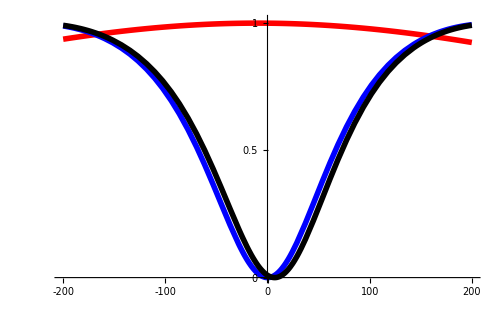
-Graphics-ET(E,E_F)

```mathematica
A7=Labeled[Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57},(T1+T2)/.{Gf->10,GM->0,γ->51,ϕ->1.57},(T1+T2)/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0,1.01}},Ticks->{{-200,-100,0,100,200},{0,0.5,1}},TicksStyle->Directive[Black,100],PlotStyle->{Directive[AbsoluteThickness[4],Opacity[1],Red],Directive[AbsoluteThickness[4],Opacity[1],Blue],Directive[AbsoluteThickness[4],Opacity[1],Black]},ImageSize->500,LabelStyle->Directive[Black,40]],{Style["E",50,Black],Style["T(E,E_F)",50,Black]},{Right,Top},RotateLabel->False]
```

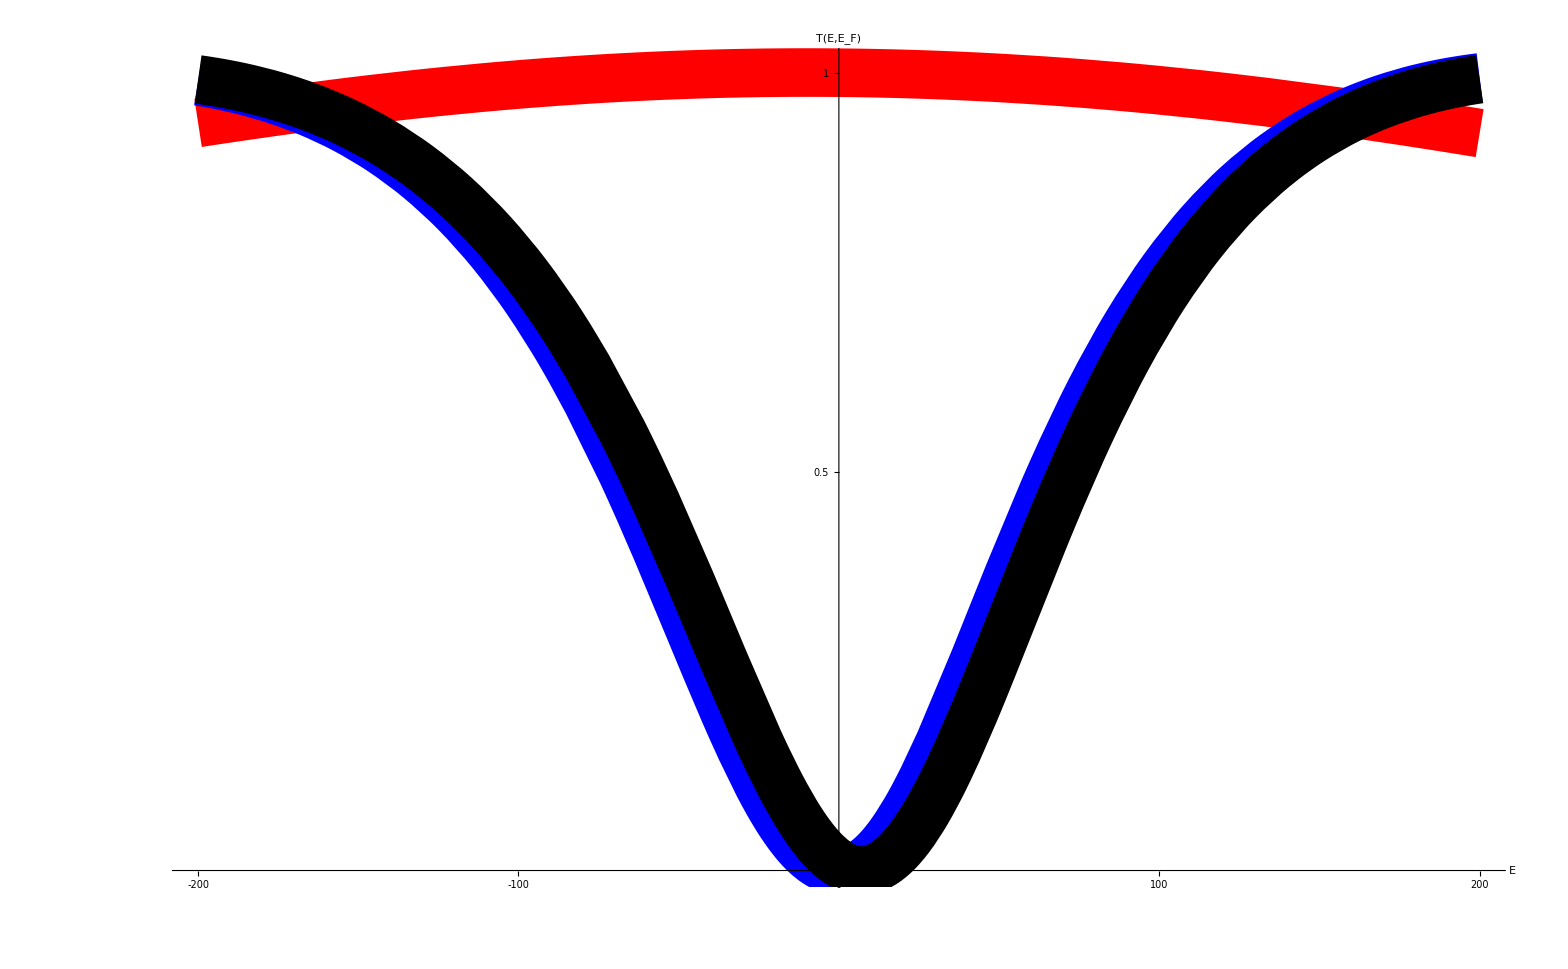

```mathematica
A8=Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57},(T1+T2)/.{Gf->10,GM->0,γ->51,ϕ->1.57},(T1+T2)/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0,1.01}},Ticks->{{-200,-100,0,100,200},{0,0.5,1}},PlotPoints->10,
AxesLabel->{Framed[Style["E",250,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->150],Framed[Style["T(E,E_F)",250,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->100]},TicksStyle->Directive[Black,150],PlotStyle->{Directive[AbsoluteThickness[35],Opacity[1],Red],Directive[AbsoluteThickness[35],Opacity[1],Blue],Directive[AbsoluteThickness[35],Opacity[1],Black]},ImageSize->5000,LabelStyle->Directive[Black,150]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->5000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[20]],Directive[Blue,AbsoluteThickness[20]],Directive[Black,AbsoluteThickness[20]]},{Style["Majorana Absent (E_M = 0, Γ = 0)",Black,150],Style["Uncoupled Majorana (E_M=0)",Black,150],Style["Coupled Majorana (E_M≠0)",Black,150]},LegendLayout->"Row",LegendMarkerSize->{400,200}],{0.999,0.20}]]
```

-Graphics-

```mathematica
Z= (GM  - G - I*γ )*(GM+G + I*γ );
x = γ*(G + I*γ )/Z;
x1 = γ*(G + I *γ)/Z;
y = GM*γ/Z;
```

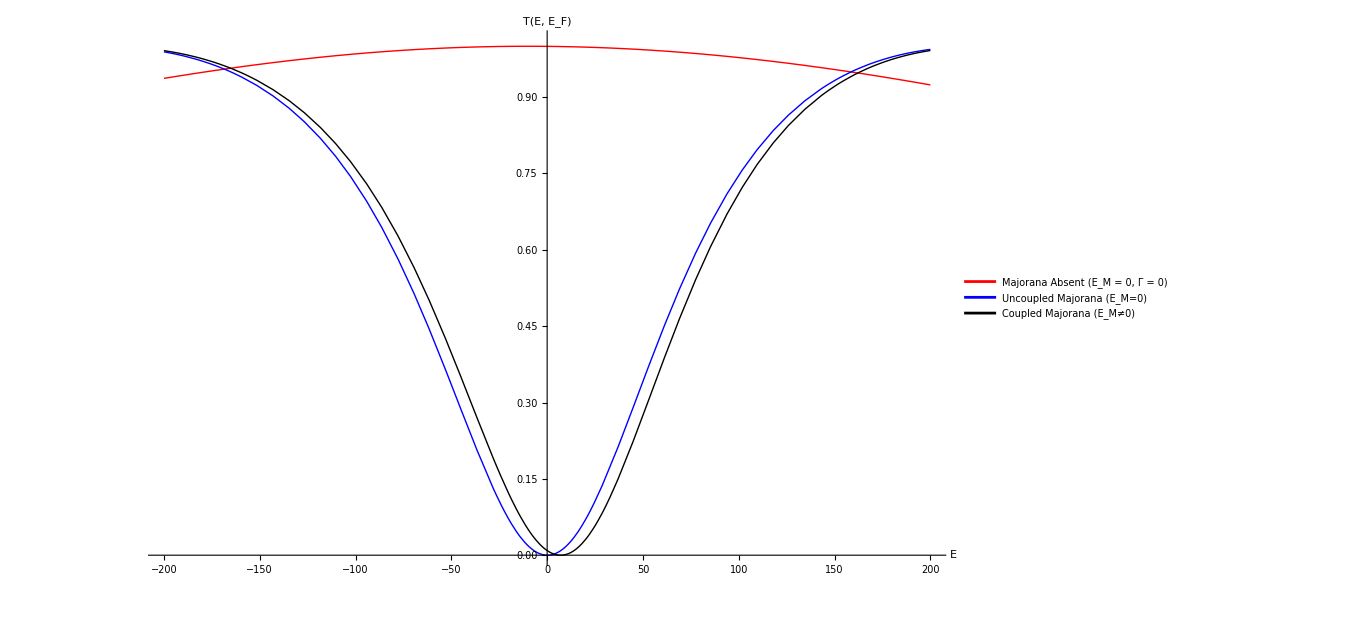

```mathematica
Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57},(T1+T2)/.{Gf->10,GM->0,γ->51,ϕ->1.57},(T1+T2)/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-200,200},PlotRange->{0,1.01},PlotStyle->{{Red,Thick},{Blue,Thick},{Black, Thick}},AxesLabel->{Style["E",24,Black],Style["T(E, E_F)",24,Black]},PlotLegends->Placed[{Style["Majorana Absent (E_M = 0, Γ = 0)",24],Style["Uncoupled Majorana (E_M=0)",24],Style["Coupled Majorana (E_M≠0)",24]},{0.8,0.15}],AxesStyle->Directive[Black, 24],ImageSize->1000]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->5000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[20]],Directive[Blue,AbsoluteThickness[20]],Directive[Black,AbsoluteThickness[20]]},{Style["Majorana Absent (E_M = 0, Γ = 0)",Black,150],Style["Uncoupled Majorana (E_M=0)",Black,150],Style["Coupled Majorana (E_M≠0)",Black,150]},LegendLayout->"Row",LegendMarkerSize->{400,200}],{0.999,0.20}]]
```

-Graphics-

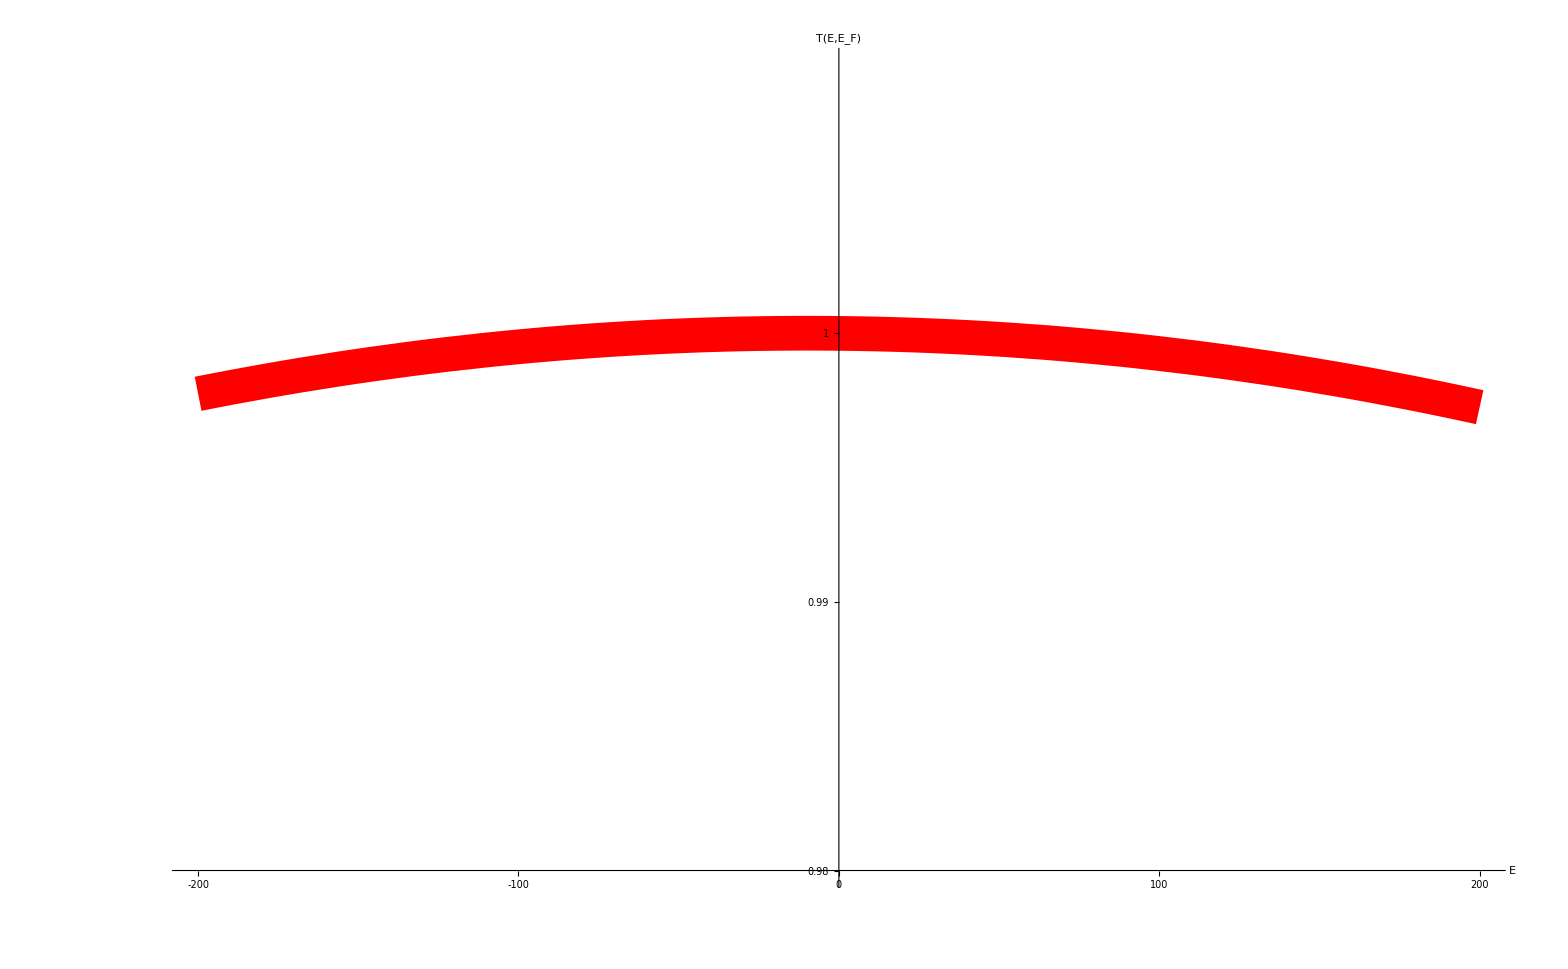

```mathematica
Ins=T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;T2=Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
A8=Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0.98,1.01}},Ticks->{{-200,-100,0,100,200},{0.98,0.99,1}},PlotPoints->10,
AxesLabel->{Framed[Style["E",230,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->150],Framed[Style["T(E,E_F)",230,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->100]},TicksStyle->Directive[Black,100],PlotStyle->{Directive[AbsoluteThickness[25],Opacity[1],Red]},ImageSize->4000,LabelStyle->Directive[Black,100]]
```

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;T2=Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
A8=Plot[{(T1+T2)/.{Gf->10,GM->0,γ->0,ϕ->1.57},(T1+T2)/.{Gf->10,GM->0,γ->51,ϕ->1.57},(T1+T2)/.{Gf->10,GM->7,γ->51,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0,1.01}},Ticks->{{-200,-100,0,100,200},{0,0.5,1}},PlotPoints->10,
AxesLabel->{Framed[Style["E",250,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->150],Framed[Style["T(E,E_F)",250,AbsoluteThickness[20],Black],FrameStyle->None,FrameMargins->100]},TicksStyle->Directive[Black,150],PlotStyle->{Directive[AbsoluteThickness[35],Opacity[1],Red],Directive[AbsoluteThickness[35],Opacity[1],Blue],Directive[AbsoluteThickness[35],Opacity[1],Black]},ImageSize->5000,LabelStyle->Directive[Black,150]]
```

```mathematica
A5=Legended[GraphicsGrid[{{A8}},ImageSize->5000],Placed[LineLegend[{Directive[Red,AbsoluteThickness[20]],Directive[Blue,AbsoluteThickness[20]],Directive[Black,AbsoluteThickness[20]]},{Style["Majorana Absent (E_M = 0, Γ = 0)",Black,150],Style["Uncoupled Majorana (E_M=0)",Black,150],Style["Coupled Majorana (E_M≠0)",Black,150]},LegendLayout->"Row",LegendMarkerSize->{400,200}],{0.999,0.20}]]
```

```mathematica
Plot[Cos[x],{x,-5,5}]
```

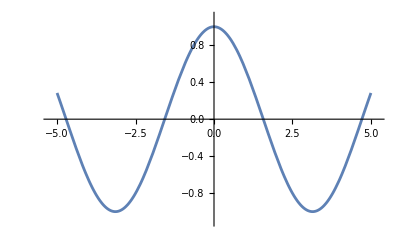

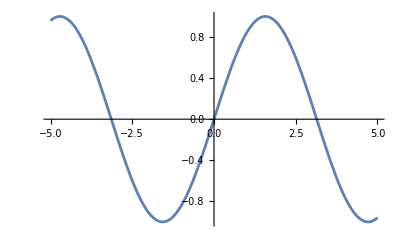

```mathematica
Plot[Sin[x],{x,-5,5}]
```

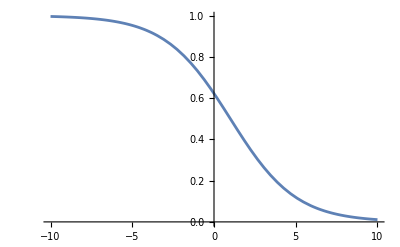

```mathematica
Plot[1/(1+Exp[(G-1)/2]),{G,-10,10}]
```

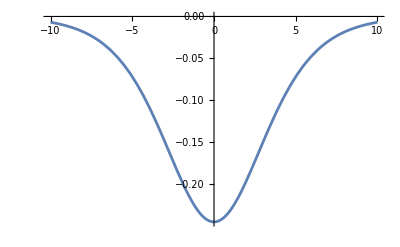

```mathematica
Plot[1/(1+Exp[(G+1)/2])-1/(1+Exp[(G-1)/2]),{G,-10,10}]
```

```mathematica
(1/(1+Exp[(G+1)/2])-1/(1+Exp[(G-1)/2]))//FullSimplify
```

-1/(1+ⅇ^(1/2 (-1+G)))+1/(1+ⅇ^((1+G)/2))

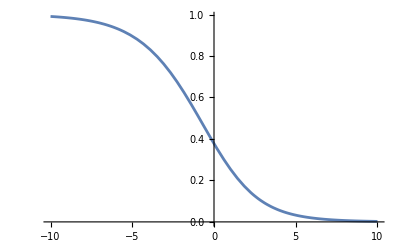

```mathematica
Plot[2/(1+Exp[G/2])-1/(1+Exp[(G-1)/2]),{G,-10,10}]
```

```mathematica
1/4+1/3+5/12
```

1

```mathematica
a=-1/2;
b=1/2;
l1=1/4;
l2=1/3;
ld=5/12;
L=1;
ke=(G+Gf)/(1000);
kh=(G-Gf)/(1000);
ke1=(G+Gf+Vg)/(1000);
kh1=(G-Gf-Vg)/(1000);
eo1u=1;
ho1d=0;
ei2u=0;
hi2d=0;
γ1=γ2=γ;
ϵ=0.5;
Vg=0;
Z= (GM  - G - I*γ )*(GM+G + I*γ );
x = γ*(G + I*γ )/Z;
x1 = γ*(G + I *γ)/Z;
y = GM*γ/Z;
P=Solve[{eiLu==(1+I x)*eoLu-y*eiRu+I x*hoLd-y*hiRd,
eoRu==y*eoLu+(1+I x1)*eiRu+y*hoLd+I x1*hiRd,
hiLd==I x*eoLu-y*eiRu+(1+I x)*hoLd-y*hiRd,
hoRd==y*eoLu+I x1*eiRu+y*hoLd+(1+I x1)*hiRd,

ei1u==-(a+b)*eo1u+p*eo3u+p*ei5u,
hi1d==-(a+b)ho1d+p*ho3d+p*hi5d,
ei3u==p*eo1u+a*eo3u+b*ei5u,
hi3d==p*ho1d+a*ho3d+b*hi5d,
eo5u==p*eo1u+b*eo3u+a*ei5u,
ho5d==p*ho1d+b*ho3d+a*hi5d,

eo2u==-(a+b)ei2u+p*ei4u+p*eo6u,
ho2d==-(a+b)hi2d+p*hi4d+p*ho6d,
eo4u==p*ei2u+a*ei4u+b*eo6u,
ho4d==p*hi2d+a*hi4d+b*ho6d,
ei6u==p*ei2u+b*ei4u+a*eo6u,
hi6d==p*hi2d+b*hi4d+a*ho6d,

ei5u==Exp[I*ke*l1]*Exp[-I*ϕ*l1]eiLu,
eoLu==Exp[I*ke*l1]*Exp[I*ϕ*l1]eo5u,
hi5d==Exp[I*kh*l1]*Exp[I*ϕ*l1]hiLd,
hoLd==Exp[I*kh*l1]*Exp[-I*ϕ*l1]ho5d,
eo6u==Exp[I*ke*l2]*Exp[I*ϕ*l2]eoRu,
eiRu==Exp[I*ke*l2]*Exp[-I*ϕ*l2]ei6u,
ho6d==Exp[I*kh*l2]*Exp[-I*ϕ*l2]hoRd,
hiRd==Exp[I*kh*l2]*Exp[I*ϕ*l2]hi6d,
eo3u==Exp[I*ke1*ld]*Exp[I*ϕ*ld]eo4u,
ei4u==Exp[I*ke1*ld]*Exp[-I*ϕ*ld]ei3u,
ho3d==Exp[I*kh1*ld]*Exp[-I*ϕ*ld]ho4d,
hi4d==Exp[I*kh1*ld]*Exp[I*ϕ*ld]hi3d}

,{eiLu,eoLu,eiRu,hoLd,hiRd,eoRu,hiLd,hoRd,ei1u,eo3u,ei5u,hi1d,ho3d,hi5d,ei3u,hi3d,eo5u,ho5d,eo2u,ei4u,eo6u,ho2d,hi4d,ho6d,eo4u,ho4d,ei6u,hi6d}];
ei1u=ei1u/.P[[1]];
hi1d=hi1d/.P[[1]]
eo2u=eo2u/.P[[1]]
ho2d=ho2d/.P[[1]]
```

(4 ⅇ^(-(ⅈ G)/6000-(ⅈ Gf)/3000-(ⅈ ϕ)/2) (2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) G^2 p^2+2 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) G^2 p^2-ⅇ^((ⅈ G)/750+(ⅈ Gf)/1200+ⅈ ϕ) G^2 p^2+ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) G^2 p^2-ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) G^2 p^2-2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM^2 p^2-2 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM^2 p^2+ⅇ^((ⅈ G)/750+(ⅈ Gf)/1200+ⅈ ϕ) GM^2 p^2-ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM^2 p^2+ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) GM^2 p^2+2 ⅈ ⅇ^((ⅈ G)/2000+ⅈ ϕ) G p^2 γ+4 ⅈ ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-ⅈ ⅇ^((ⅈ G)/750+(ⅈ Gf)/1200+ⅈ ϕ) G p^2 γ+ⅈ ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) G p^2 γ-2 ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) G p^2 γ-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000) GM p^2 γ-ⅇ^((ⅈ G)/1000+(3 ⅈ Gf)/2000) GM p^2 γ-2 ⅇ^((ⅈ G)/6000+(ⅈ Gf)/3000+2 ⅈ ϕ) GM p^2 γ-ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ+ⅇ^((ⅈ G)/1000+(7 ⅈ Gf)/6000+2 ⅈ ϕ) GM p^2 γ-2 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2+ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) p^2 γ^2))/(γ (-2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) G-ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1200) G-ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G-2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM-4 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM+ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1500+ⅈ ϕ) GM-ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM-2 ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM+2 ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) γ+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ))+(2 ⅇ^(-(ⅈ G)/2400-(7 ⅈ Gf)/12000-(3 ⅈ ϕ)/4) p (4 ⅇ^((ⅈ G)/2000+ⅈ ϕ) G^2+4 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) G^2+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+ⅈ ϕ) G^2+2 ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) G^2-ⅇ^((ⅈ G)/750+(ⅈ Gf)/1200+ⅈ ϕ) G^2+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+ⅈ ϕ) G^2+2 ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) G^2+ⅇ^((ⅈ G)/600+(7 ⅈ Gf)/6000+ⅈ ϕ) G^2-ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) G^2+ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/600+ⅈ ϕ) G^2-4 ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM^2-4 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM^2-2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+ⅈ ϕ) GM^2-2 ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM^2+ⅇ^((ⅈ G)/750+(ⅈ Gf)/1200+ⅈ ϕ) GM^2-2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+ⅈ ϕ) GM^2-2 ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM^2-ⅇ^((ⅈ G)/600+(7 ⅈ Gf)/6000+ⅈ ϕ) GM^2+ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) GM^2-ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/600+ⅈ ϕ) GM^2+4 ⅈ ⅇ^((ⅈ G)/2000+ⅈ ϕ) G γ+8 ⅈ ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) G γ-ⅈ ⅇ^((ⅈ G)/750+(ⅈ Gf)/1200+ⅈ ϕ) G γ+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+ⅈ ϕ) G γ+2 ⅈ ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) G γ-ⅈ ⅇ^((ⅈ G)/600+(7 ⅈ Gf)/6000+ⅈ ϕ) G γ-2 ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) G γ-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000) GM γ-ⅇ^((ⅈ G)/1000+(3 ⅈ Gf)/2000) GM γ-4 ⅇ^((ⅈ G)/6000+(ⅈ Gf)/3000+2 ⅈ ϕ) GM γ-2 ⅇ^((ⅈ G)/1500+(ⅈ Gf)/1200+2 ⅈ ϕ) GM γ-2 ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/1000+(7 ⅈ Gf)/6000+2 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/1000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM γ-ⅇ^((ⅈ G)/750+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM γ-4 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) γ^2+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+ⅈ ϕ) γ^2+ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/750+3 ⅈ ϕ) γ^2) (-((1/2 ⅇ^((7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) p (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2))+((ⅇ^((11 ⅈ (G+Gf))/6000-(5 ⅈ ϕ)/6) GM p γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^((3 ⅈ (G+Gf))/2000+(ⅈ ϕ)/6) p (G+ⅈ γ) γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-(((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(1/4 ⅇ^((ⅈ (G-Gf))/4000+(7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/3) p (-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+1/2 ⅇ^((7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) p (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-((-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((13 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))/(γ (-2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) G-ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1200) G-ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G-2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM-4 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM+ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1500+ⅈ ϕ) GM-ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM-2 ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM+2 ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) γ+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ) (-((-(((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))) ((-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000-(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^(1/800 ⅈ (G+Gf)-(ⅈ ϕ)/12) (G+ⅈ γ) γ (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))-(-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/3000-(ⅈ ϕ)/3) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(-(((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/3000-(ⅈ ϕ)/3) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/4 ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/3000-(7 ⅈ ϕ)/12) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))) (-((-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((13 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))

(4 ⅇ^(-(5 ⅈ ϕ)/12) (ⅇ^((3 ⅈ G)/4000+(7 ⅈ Gf)/12000) G p^2+ⅇ^((17 ⅈ G)/12000+(ⅈ Gf)/800) G p^2-ⅇ^((7 ⅈ G)/12000+(ⅈ Gf)/12000+2 ⅈ ϕ) G p^2-2 ⅇ^((ⅈ G)/12000+(7 ⅈ Gf)/12000+2 ⅈ ϕ) G p^2+ⅇ^((17 ⅈ G)/12000+(11 ⅈ Gf)/12000+2 ⅈ ϕ) G p^2+2 ⅇ^((11 ⅈ G)/12000+(17 ⅈ Gf)/12000+2 ⅈ ϕ) G p^2-ⅈ ⅇ^((ⅈ G)/2400+(ⅈ Gf)/4000+ⅈ ϕ) GM p^2-ⅈ ⅇ^((11 ⅈ G)/12000+(ⅈ Gf)/2400+ⅈ ϕ) GM p^2-2 ⅈ ⅇ^((ⅈ G)/2400+(11 ⅈ Gf)/12000+ⅈ ϕ) GM p^2+ⅈ ⅇ^((ⅈ G)/800+(13 ⅈ Gf)/12000+ⅈ ϕ) GM p^2-ⅈ ⅇ^((19 ⅈ G)/12000+(13 ⅈ Gf)/12000+ⅈ ϕ) GM p^2-2 ⅈ ⅇ^((13 ⅈ G)/12000+(19 ⅈ Gf)/12000+ⅈ ϕ) GM p^2+ⅈ ⅇ^((3 ⅈ G)/4000+(7 ⅈ Gf)/12000) p^2 γ-2 ⅈ ⅇ^((ⅈ G)/12000+(7 ⅈ Gf)/12000+2 ⅈ ϕ) p^2 γ+2 ⅈ ⅇ^((11 ⅈ G)/12000+(17 ⅈ Gf)/12000+2 ⅈ ϕ) p^2 γ))/(2 ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1200) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM-4 ⅈ ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM+ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1500+ⅈ ϕ) GM-ⅈ ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM-2 ⅈ ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM+2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) γ+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ)+(2 ⅇ^(-(ⅈ G)/6000-(ⅈ Gf)/6000-(2 ⅈ ϕ)/3) p (ⅇ^((ⅈ G)/1500+(ⅈ Gf)/2000) G+ⅇ^((ⅈ G)/750+(7 ⅈ Gf)/6000) G-2 ⅇ^((ⅈ G)/2000+2 ⅈ ϕ) G-4 ⅇ^((ⅈ Gf)/2000+2 ⅈ ϕ) G-ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G+ⅇ^((ⅈ G)/750+(ⅈ Gf)/1200+2 ⅈ ϕ) G-2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G+2 ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000+ⅈ ϕ) GM-ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/3000+ⅈ ϕ) GM-ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1500+ⅈ ϕ) GM-2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/1200+ⅈ ϕ) GM+ⅈ ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1000+ⅈ ϕ) GM-ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1000+ⅈ ϕ) GM-2 ⅈ ⅇ^((ⅈ G)/1000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM+ⅈ ⅇ^((ⅈ G)/1500+(ⅈ Gf)/2000) γ-4 ⅈ ⅇ^((ⅈ Gf)/2000+2 ⅈ ϕ) γ+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) γ+2 ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/750+2 ⅈ ϕ) γ) (-((1/2 ⅇ^((7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) p (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2))+((ⅇ^((11 ⅈ (G+Gf))/6000-(5 ⅈ ϕ)/6) GM p γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^((3 ⅈ (G+Gf))/2000+(ⅈ ϕ)/6) p (G+ⅈ γ) γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-(((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(1/4 ⅇ^((ⅈ (G-Gf))/4000+(7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/3) p (-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+1/2 ⅇ^((7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) p (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-((-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((13 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))/((2 ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1200) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM-4 ⅈ ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM+ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1500+ⅈ ϕ) GM-ⅈ ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM-2 ⅈ ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM+2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) γ+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ) (-((-(((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))) ((-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000-(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^(1/800 ⅈ (G+Gf)-(ⅈ ϕ)/12) (G+ⅈ γ) γ (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))-(-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/3000-(ⅈ ϕ)/3) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(-(((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/3000-(ⅈ ϕ)/3) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/4 ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/3000-(7 ⅈ ϕ)/12) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))) (-((-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((13 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))

-((4 ⅇ^(-(7 ⅈ G)/12000-(ⅈ Gf)/2400-(ⅈ ϕ)/12) (2 ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) G^2 p^2-2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1200+ⅈ ϕ) G^2 p^2-4 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2-ⅈ ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2-ⅈ ⅇ^((7 ⅈ G)/6000+(7 ⅈ Gf)/6000+ⅈ ϕ) G^2 p^2+ⅈ ⅇ^((ⅈ G)/750+(ⅈ Gf)/750+ⅈ ϕ) G^2 p^2-2 ⅈ ⅇ^((ⅈ G)/1500+(ⅈ Gf)/600+ⅈ ϕ) G^2 p^2+2 ⅈ ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) G^2 p^2-2 ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) GM^2 p^2+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1200+ⅈ ϕ) GM^2 p^2+4 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2+ⅈ ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2+ⅈ ⅇ^((7 ⅈ G)/6000+(7 ⅈ Gf)/6000+ⅈ ϕ) GM^2 p^2-ⅈ ⅇ^((ⅈ G)/750+(ⅈ Gf)/750+ⅈ ϕ) GM^2 p^2+2 ⅈ ⅇ^((ⅈ G)/1500+(ⅈ Gf)/600+ⅈ ϕ) GM^2 p^2-2 ⅈ ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) G p^2 γ+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1200+ⅈ ϕ) G p^2 γ+8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ+2 ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ-ⅇ^((ⅈ G)/750+(ⅈ Gf)/750+ⅈ ϕ) G p^2 γ+2 ⅇ^((ⅈ G)/1500+(ⅈ Gf)/600+ⅈ ϕ) G p^2 γ-4 ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) G p^2 γ-ⅈ ⅇ^((11 ⅈ G)/6000+(7 ⅈ Gf)/6000) GM p^2 γ+ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000) GM p^2 γ+2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500) GM p^2 γ+2 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM p^2 γ+ⅈ ⅇ^((ⅈ G)/600+(ⅈ Gf)/1500+2 ⅈ ϕ) GM p^2 γ-ⅈ ⅇ^((11 ⅈ G)/6000+(ⅈ Gf)/1200+2 ⅈ ϕ) GM p^2 γ-2 ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) p^2 γ^2+4 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) p^2 γ^2+ⅈ ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) p^2 γ^2-2 ⅈ ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) p^2 γ^2))/(γ (2 ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1200) G+ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G-2 ⅈ ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM-4 ⅈ ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM+ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1500+ⅈ ϕ) GM-ⅈ ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM-2 ⅈ ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM+2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) γ+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ)))+(2 ⅇ^(-(ⅈ G)/1200-(ⅈ Gf)/1500-(ⅈ ϕ)/3) p (4 ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) G^2-4 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G^2+2 ⅇ^((ⅈ G)/750+(ⅈ Gf)/1500+ⅈ ϕ) G^2+2 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1200+ⅈ ϕ) G^2-8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G^2-2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G^2-ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) G^2-2 ⅇ^((7 ⅈ G)/6000+(7 ⅈ Gf)/6000+ⅈ ϕ) G^2+ⅇ^((ⅈ G)/750+(ⅈ Gf)/750+ⅈ ϕ) G^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/750+ⅈ ϕ) G^2-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2-4 ⅇ^((ⅈ G)/1500+(ⅈ Gf)/600+ⅈ ϕ) G^2-ⅇ^((ⅈ G)/600+(ⅈ Gf)/600+ⅈ ϕ) G^2+2 ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) G^2-2 ⅇ^((7 ⅈ G)/6000+(13 ⅈ Gf)/6000+ⅈ ϕ) G^2-4 ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) GM^2+4 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM^2-2 ⅇ^((ⅈ G)/750+(ⅈ Gf)/1500+ⅈ ϕ) GM^2-2 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1200+ⅈ ϕ) GM^2+8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM^2+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) GM^2+ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) GM^2+2 ⅇ^((7 ⅈ G)/6000+(7 ⅈ Gf)/6000+ⅈ ϕ) GM^2-ⅇ^((ⅈ G)/750+(ⅈ Gf)/750+ⅈ ϕ) GM^2-ⅇ^((ⅈ G)/500+(ⅈ Gf)/750+ⅈ ϕ) GM^2+4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2+4 ⅇ^((ⅈ G)/1500+(ⅈ Gf)/600+ⅈ ϕ) GM^2+ⅇ^((ⅈ G)/600+(ⅈ Gf)/600+ⅈ ϕ) GM^2-2 ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) GM^2+2 ⅇ^((7 ⅈ G)/6000+(13 ⅈ Gf)/6000+ⅈ ϕ) GM^2+8 ⅈ ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) G γ-4 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G γ+2 ⅈ ⅇ^((ⅈ G)/750+(ⅈ Gf)/1500+ⅈ ϕ) G γ+2 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/1200+ⅈ ϕ) G γ-16 ⅈ ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) G γ-2 ⅈ ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) G γ+ⅈ ⅇ^((ⅈ G)/750+(ⅈ Gf)/750+ⅈ ϕ) G γ-4 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G γ-4 ⅈ ⅇ^((ⅈ G)/1500+(ⅈ Gf)/600+ⅈ ϕ) G γ+ⅈ ⅇ^((ⅈ G)/600+(ⅈ Gf)/600+ⅈ ϕ) G γ+4 ⅈ ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) G γ-ⅇ^((11 ⅈ G)/6000+(7 ⅈ Gf)/6000) GM γ+ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000) GM γ+2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500) GM γ+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM γ+2 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM γ+2 ⅇ^((ⅈ G)/600+(ⅈ Gf)/1500+2 ⅈ ϕ) GM γ-ⅇ^((11 ⅈ G)/6000+(ⅈ Gf)/1200+2 ⅈ ϕ) GM γ+ⅇ^((11 ⅈ G)/6000+(7 ⅈ Gf)/6000+2 ⅈ ϕ) GM γ+ⅇ^((13 ⅈ G)/6000+(7 ⅈ Gf)/6000+2 ⅈ ϕ) GM γ-ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM γ-2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1200+(ⅈ Gf)/6000+ⅈ ϕ) γ^2+8 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/600+(ⅈ Gf)/1000+ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/1200+(11 ⅈ Gf)/6000+ⅈ ϕ) γ^2-ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+3 ⅈ ϕ) γ^2) (-((1/2 ⅇ^((7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) p (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2))+((ⅇ^((11 ⅈ (G+Gf))/6000-(5 ⅈ ϕ)/6) GM p γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^((3 ⅈ (G+Gf))/2000+(ⅈ ϕ)/6) p (G+ⅈ γ) γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-(((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(1/4 ⅇ^((ⅈ (G-Gf))/4000+(7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/3) p (-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+1/2 ⅇ^((7 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) p (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-((-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((13 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))/(γ (2 ⅈ ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) G+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1200) G+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/2000+2 ⅈ ϕ) G+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) G+2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) GM+4 ⅇ^((ⅈ Gf)/2000+ⅈ ϕ) GM-ⅇ^((ⅈ G)/1200+(ⅈ Gf)/1500+ⅈ ϕ) GM+ⅇ^((7 ⅈ G)/6000+(ⅈ Gf)/1500+ⅈ ϕ) GM+2 ⅇ^((ⅈ G)/1500+(7 ⅈ Gf)/6000+ⅈ ϕ) GM-2 ⅇ^((ⅈ G)/3000+(ⅈ Gf)/6000) γ-2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ) (-((-(((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/2 ⅇ^((ⅈ (G-Gf))/4000-(ⅈ ϕ)/4) (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))) ((-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G+Gf))/4000-(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅈ ⅇ^(1/800 ⅈ (G+Gf)-(ⅈ ϕ)/12) (G+ⅈ γ) γ (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))-(-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/3000-(ⅈ ϕ)/3) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))))+(-(((ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ (-1/4 ⅇ^((3 ⅈ (G-Gf))/4000+(3 ⅈ ϕ)/4)-(ⅇ^((11 ⅈ (G-Gf))/12000-(ⅈ ϕ)/4) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅈ ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) (G+ⅈ γ) γ (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅈ ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM (G+ⅈ γ) γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-1/2 ⅇ^((ⅈ (G+Gf))/3000-(ⅈ ϕ)/3) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-(ⅇ^((11 ⅈ (G-Gf))/12000+(ⅈ (G+Gf))/1200-(7 ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+1/4 ⅇ^((ⅈ (G-Gf))/4000+(ⅈ (G+Gf))/3000-(7 ⅈ ϕ)/12) (1-1/2 ⅇ^((ⅈ (G-Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))) (-1+1/2 ⅇ^((ⅈ (G+Gf))/2000) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))) (-((-(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)+(ⅇ^((7 ⅈ (G+Gf))/4000-(ⅈ ϕ)/12) (G+ⅈ γ)^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)) ((ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM^2 γ^2)/(16 (-G+GM-ⅈ γ)^2 (G+GM+ⅈ γ)^2)-(-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) (-1/4 ⅇ^((ⅈ (G-Gf))/1500-(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))+(-(ⅈ ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) G γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/3000+(ⅈ (G+Gf))/1200) GM γ)/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((ⅈ (G-Gf))/1200+(ⅈ (G+Gf))/1200) GM γ)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))+(ⅇ^((ⅈ (G-Gf))/1500+(ⅈ (G+Gf))/1200-ⅈ ϕ) γ^2)/(16 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))) ((ⅈ ⅇ^((11 ⅈ (G+Gf))/12000+(ⅈ ϕ)/4) (G+ⅈ γ) γ (-1/4 ⅇ^((ⅈ (G+Gf))/1500+(2 ⅈ ϕ)/3)+(ⅇ^((ⅈ (G+Gf))/1200-(ⅈ ϕ)/3) GM γ)/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))/(4 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))-(ⅇ^((13 ⅈ (G+Gf))/12000-(ⅈ ϕ)/12) GM γ (1-1/2 ⅇ^((ⅈ (G+Gf))/1500) (-1-(ⅈ (G+ⅈ γ) γ)/((-G+GM-ⅈ γ) (G+GM+ⅈ γ)))))/(8 (-G+GM-ⅈ γ) (G+GM+ⅈ γ))))))

```mathematica
Te=Refine[eo2u]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ (G+Gf+1400 ϕ))/2400) (ⅇ^((7 ⅈ G)/6000+ⅈ ϕ) (G^2-GM^2)+2 ⅇ^((ⅈ (7 G+6 Gf+6000 ϕ))/6000) (G^2-GM^2)+4 ⅇ^((ⅈ (7 G+14 Gf+6000 ϕ))/6000) (G^2-GM^2)+2 ⅇ^((ⅈ (7 G+8 (Gf+750 ϕ)))/6000) (G^2-GM^2)+ⅇ^((ⅈ (4 G+3 Gf+2000 ϕ))/2000) (-G^2+GM^2)+ⅇ^((ⅈ (2 G+Gf))/1200) GM γ+ⅇ^((ⅈ (6 G+Gf))/6000) GM γ+ⅇ^((ⅈ (9 G+4 Gf))/6000) GM γ+ⅇ^((ⅈ (13 G+8 Gf))/6000) GM γ-ⅇ^((ⅈ (2 G+Gf+2400 ϕ))/1200) GM γ+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/2000) GM γ-ⅇ^((ⅈ (6 G+Gf+12000 ϕ))/6000) GM γ-ⅇ^((ⅈ (8 G+Gf+12000 ϕ))/6000) GM γ+2 ⅇ^((ⅈ (10 G+9 Gf+12000 ϕ))/6000) GM γ+4 ⅇ^((ⅈ (6 G+13 Gf+12000 ϕ))/6000) GM γ+2 ⅇ^((ⅈ (9 G+10 (Gf+1200 ϕ)))/6000) GM γ-4 ⅇ^((ⅈ (G+8 (Gf+1500 ϕ)))/6000) GM γ-ⅇ^((ⅈ (11 G+8 (Gf+1500 ϕ)))/6000) GM γ-ⅇ^((ⅈ (13 G+8 (Gf+1500 ϕ)))/6000) GM γ+ⅇ^((ⅈ (13 G+6 (Gf+2000 ϕ)))/6000) GM γ-2 ⅇ^((ⅈ (4 G+5 (Gf+2400 ϕ)))/6000) GM γ-2 ⅇ^((ⅈ (5 G+4 (Gf+3000 ϕ)))/6000) GM γ-ⅇ^((ⅈ (9 G+4 (Gf+3000 ϕ)))/6000) GM γ+ⅇ^((ⅈ (12 G+7 Gf+18000 ϕ))/6000) γ^2-ⅇ^((ⅈ (7 G+2 (Gf+9000 ϕ)))/6000) γ^2+ⅇ^((ⅈ (10 G+3 Gf+6000 ϕ))/6000) (G^2-GM^2-ⅈ G γ)+ⅇ^((ⅈ (11 G+4 Gf+6000 ϕ))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (10 G+11 Gf+6000 ϕ))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (11 G+10 (Gf+600 ϕ)))/6000) (G^2-GM^2-ⅈ G γ)+ⅇ^((ⅈ (3 G+2 Gf+2000 ϕ))/2000) (-G^2+GM^2-ⅈ G γ)+ⅇ^((ⅈ (8 G+5 Gf+6000 ϕ))/6000) (-G^2+GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (4 G+3 Gf+6000 ϕ))/6000) (G^2-GM^2+ⅈ G γ)+2 ⅇ^((ⅈ (3 G+4 Gf+6000 ϕ))/6000) (G^2-GM^2+ⅈ G γ)+4 ⅇ^((ⅈ (4 G+11 Gf+6000 ϕ))/6000) (G^2-GM^2+ⅈ G γ)+4 ⅇ^((ⅈ (3 G+10 (Gf+600 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)+ⅇ^((ⅈ (14 G+7 Gf+6000 ϕ))/6000) (G^2-GM^2-2 ⅈ G γ-γ^2)+4 ⅇ^((7 ⅈ Gf)/6000+ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+2 ⅇ^((ⅈ (6 G+7 Gf+6000 ϕ))/6000) (G^2-GM^2+γ^2)+2 ⅇ^((ⅈ (8 G+7 Gf+6000 ϕ))/6000) (G^2-GM^2+γ^2)+ⅇ^((ⅈ (5 G+2 Gf+6000 ϕ))/6000) (-G^2+GM^2-2 ⅈ G γ+γ^2)))/(4 ⅇ^((7 ⅈ G)/6000+2 ⅈ ϕ) (G^2-GM^2)+4 ⅇ^((ⅈ (7 G+14 Gf+12000 ϕ))/6000) (G^2-GM^2)+4 ⅇ^((ⅈ (7 G+8 (Gf+1500 ϕ)))/6000) (G^2-GM^2)+4 ⅇ^((ⅈ (7 G+6 (Gf+2000 ϕ)))/6000) (G^2-GM^2)+ⅇ^((ⅈ (4 G+3 Gf+4000 ϕ))/2000) (-G^2+GM^2)+ⅇ^((ⅈ (12 G+5 (Gf+2400 ϕ)))/6000) (-G^2+GM^2)+2 ⅇ^((ⅈ (2 G+Gf+1200 ϕ))/1200) GM γ-2 ⅇ^((ⅈ (2 G+Gf+3600 ϕ))/1200) GM γ+4 ⅇ^((ⅈ (6 G+Gf+6000 ϕ))/6000) GM γ+2 ⅇ^((ⅈ (9 G+4 Gf+6000 ϕ))/6000) GM γ-ⅇ^((ⅈ (11 G+6 Gf+6000 ϕ))/6000) GM γ-ⅇ^((ⅈ (13 G+6 Gf+6000 ϕ))/6000) GM γ-2 ⅇ^((ⅈ (10 G+9 Gf+6000 ϕ))/6000) GM γ-4 ⅇ^((ⅈ (6 G+13 Gf+6000 ϕ))/6000) GM γ-4 ⅇ^((ⅈ (6 G+Gf+18000 ϕ))/6000) GM γ+4 ⅇ^((ⅈ (6 G+13 Gf+18000 ϕ))/6000) GM γ-2 ⅇ^((ⅈ (9 G+10 (Gf+600 ϕ)))/6000) GM γ+ⅇ^((ⅈ (11 G+8 (Gf+750 ϕ)))/6000) GM γ+ⅇ^((ⅈ (13 G+8 (Gf+750 ϕ)))/6000) GM γ+2 ⅇ^((ⅈ (9 G+10 (Gf+1800 ϕ)))/6000) GM γ+2 ⅇ^((ⅈ (10 G+9 (Gf+2000 ϕ)))/6000) GM γ-ⅇ^((ⅈ (11 G+8 (Gf+2250 ϕ)))/6000) GM γ-ⅇ^((ⅈ (13 G+8 (Gf+2250 ϕ)))/6000) GM γ+ⅇ^((ⅈ (11 G+6 (Gf+3000 ϕ)))/6000) GM γ+ⅇ^((ⅈ (13 G+6 (Gf+3000 ϕ)))/6000) GM γ-2 ⅇ^((ⅈ (9 G+4 (Gf+4500 ϕ)))/6000) GM γ+ⅇ^((ⅈ (12 G+7 Gf))/6000) γ^2+ⅇ^((ⅈ (12 G+7 Gf+24000 ϕ))/6000) γ^2+2 ⅇ^((ⅈ (10 G+11 Gf+12000 ϕ))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (11 G+10 (Gf+1200 ϕ)))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (11 G+4 (Gf+3000 ϕ)))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (10 G+3 (Gf+4000 ϕ)))/6000) (G^2-GM^2-ⅈ G γ)-2 ⅇ^((ⅈ (3 G+2 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)-2 ⅇ^((ⅈ (8 G+9 Gf+12000 ϕ))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (4 G+11 Gf+12000 ϕ))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (3 G+10 (Gf+1200 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)-2 ⅇ^((ⅈ (9 G+8 (Gf+1500 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)-2 ⅇ^((ⅈ (8 G+5 (Gf+2400 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (3 G+4 (Gf+3000 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (4 G+3 (Gf+4000 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)+ⅇ^((ⅈ (14 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2-2 ⅈ G γ-γ^2)+16 ⅇ^((7 ⅈ Gf)/6000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+ⅇ^((ⅈ (10 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2+2 ⅈ G γ-γ^2)-4 ⅇ^((ⅈ (5 G+12 (Gf+1000 ϕ)))/6000) (G^2-GM^2+2 ⅈ G γ-γ^2)-4 ⅇ^((ⅈ (5 G+2 (Gf+6000 ϕ)))/6000) (G^2-GM^2+2 ⅈ G γ-γ^2)+4 ⅇ^((ⅈ (6 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2+γ^2)+4 ⅇ^((ⅈ (8 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2+γ^2))

```mathematica
Th=Refine[ho2d]/.{p->Sqrt[1/2]}//Simplify
```

-((2 ⅇ^((ⅈ (7 G+Gf+11000 ϕ))/12000) γ (ⅈ ⅇ^((ⅈ (G+Gf))/1000) G+2 ⅈ ⅇ^((ⅈ (G+2 Gf))/1000) G-ⅈ ⅇ^((ⅈ (11 G+7 Gf))/6000) G+2 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G+ⅈ ⅇ^((ⅈ (3 G+4 Gf+6000 ϕ))/3000) G-ⅈ ⅇ^((ⅈ (11 G+5 (Gf+2400 ϕ)))/6000) G+4 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM-ⅇ^(1/750 ⅈ (G+Gf+750 ϕ)) GM-ⅇ^((ⅈ (2 G+Gf+1000 ϕ))/1000) GM+2 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) GM-ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM+ⅇ^((ⅈ (5 G+3 Gf+3000 ϕ))/3000) GM-2 ⅇ^((ⅈ (5 G+Gf+6000 ϕ))/6000) GM-ⅇ^((ⅈ (9 G+5 Gf+6000 ϕ))/6000) GM-ⅇ^((ⅈ (5 G+7 Gf+6000 ϕ))/6000) GM+ⅇ^((ⅈ (7 G+7 Gf+6000 ϕ))/6000) GM-2 ⅇ^((ⅈ (5 G+11 Gf+6000 ϕ))/6000) GM+2 ⅇ^((ⅈ (2 G+5 (Gf+600 ϕ)))/3000) GM-ⅇ^((ⅈ (4 G+5 (Gf+600 ϕ)))/3000) GM+2 ⅈ ⅇ^((ⅈ (G+3 Gf))/2000) (G+ⅈ γ)+2 ⅈ ⅇ^((ⅈ (G+2 Gf+6000 ϕ))/3000) (G+ⅈ γ)+ⅇ^((ⅈ (2 G+Gf))/1500) (-ⅈ G+γ)+ⅇ^((ⅈ (7 G+9 Gf+12000 ϕ))/6000) (-ⅈ G+γ)+ⅇ^((3 ⅈ (G+Gf))/2000) (ⅈ G+γ)+ⅇ^((ⅈ (5 G+2 Gf+6000 ϕ))/3000) (ⅈ G+γ)))/(4 ⅇ^((7 ⅈ G)/6000+2 ⅈ ϕ) (G^2-GM^2)+4 ⅇ^((ⅈ (7 G+14 Gf+12000 ϕ))/6000) (G^2-GM^2)+4 ⅇ^((ⅈ (7 G+8 (Gf+1500 ϕ)))/6000) (G^2-GM^2)+4 ⅇ^((ⅈ (7 G+6 (Gf+2000 ϕ)))/6000) (G^2-GM^2)+ⅇ^((ⅈ (4 G+3 Gf+4000 ϕ))/2000) (-G^2+GM^2)+ⅇ^((ⅈ (12 G+5 (Gf+2400 ϕ)))/6000) (-G^2+GM^2)+2 ⅇ^((ⅈ (2 G+Gf+1200 ϕ))/1200) GM γ-2 ⅇ^((ⅈ (2 G+Gf+3600 ϕ))/1200) GM γ+4 ⅇ^((ⅈ (6 G+Gf+6000 ϕ))/6000) GM γ+2 ⅇ^((ⅈ (9 G+4 Gf+6000 ϕ))/6000) GM γ-ⅇ^((ⅈ (11 G+6 Gf+6000 ϕ))/6000) GM γ-ⅇ^((ⅈ (13 G+6 Gf+6000 ϕ))/6000) GM γ-2 ⅇ^((ⅈ (10 G+9 Gf+6000 ϕ))/6000) GM γ-4 ⅇ^((ⅈ (6 G+13 Gf+6000 ϕ))/6000) GM γ-4 ⅇ^((ⅈ (6 G+Gf+18000 ϕ))/6000) GM γ+4 ⅇ^((ⅈ (6 G+13 Gf+18000 ϕ))/6000) GM γ-2 ⅇ^((ⅈ (9 G+10 (Gf+600 ϕ)))/6000) GM γ+ⅇ^((ⅈ (11 G+8 (Gf+750 ϕ)))/6000) GM γ+ⅇ^((ⅈ (13 G+8 (Gf+750 ϕ)))/6000) GM γ+2 ⅇ^((ⅈ (9 G+10 (Gf+1800 ϕ)))/6000) GM γ+2 ⅇ^((ⅈ (10 G+9 (Gf+2000 ϕ)))/6000) GM γ-ⅇ^((ⅈ (11 G+8 (Gf+2250 ϕ)))/6000) GM γ-ⅇ^((ⅈ (13 G+8 (Gf+2250 ϕ)))/6000) GM γ+ⅇ^((ⅈ (11 G+6 (Gf+3000 ϕ)))/6000) GM γ+ⅇ^((ⅈ (13 G+6 (Gf+3000 ϕ)))/6000) GM γ-2 ⅇ^((ⅈ (9 G+4 (Gf+4500 ϕ)))/6000) GM γ+ⅇ^((ⅈ (12 G+7 Gf))/6000) γ^2+ⅇ^((ⅈ (12 G+7 Gf+24000 ϕ))/6000) γ^2+2 ⅇ^((ⅈ (10 G+11 Gf+12000 ϕ))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (11 G+10 (Gf+1200 ϕ)))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (11 G+4 (Gf+3000 ϕ)))/6000) (G^2-GM^2-ⅈ G γ)+2 ⅇ^((ⅈ (10 G+3 (Gf+4000 ϕ)))/6000) (G^2-GM^2-ⅈ G γ)-2 ⅇ^((ⅈ (3 G+2 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)-2 ⅇ^((ⅈ (8 G+9 Gf+12000 ϕ))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (4 G+11 Gf+12000 ϕ))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (3 G+10 (Gf+1200 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)-2 ⅇ^((ⅈ (9 G+8 (Gf+1500 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)-2 ⅇ^((ⅈ (8 G+5 (Gf+2400 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (3 G+4 (Gf+3000 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (4 G+3 (Gf+4000 ϕ)))/6000) (G^2-GM^2+ⅈ G γ)+ⅇ^((ⅈ (14 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2-2 ⅈ G γ-γ^2)+16 ⅇ^((7 ⅈ Gf)/6000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+ⅇ^((ⅈ (10 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2+2 ⅈ G γ-γ^2)-4 ⅇ^((ⅈ (5 G+12 (Gf+1000 ϕ)))/6000) (G^2-GM^2+2 ⅈ G γ-γ^2)-4 ⅇ^((ⅈ (5 G+2 (Gf+6000 ϕ)))/6000) (G^2-GM^2+2 ⅈ G γ-γ^2)+4 ⅇ^((ⅈ (6 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2+γ^2)+4 ⅇ^((ⅈ (8 G+7 Gf+12000 ϕ))/6000) (G^2-GM^2+γ^2)))

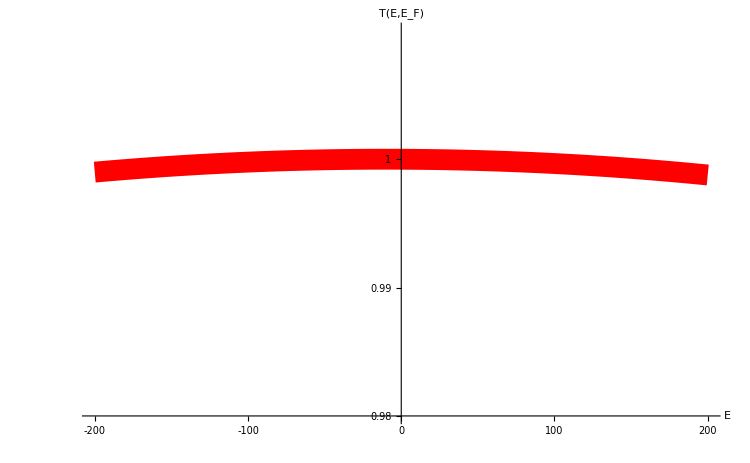

```mathematica
A8=Plot[{(Abs[Te]^2+Abs[Th]^2)/.{Gf->10,GM->0,γ->0,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0.98,1.01}},Ticks->{{-200,-100,0,100,200},{0.98,0.99,1}},PlotPoints->10,
AxesLabel->{Framed[Style["E",25,AbsoluteThickness[15],Black],FrameStyle->None,FrameMargins->10],Framed[Style["T(E,E_F)",25,AbsoluteThickness[15],Black],FrameStyle->None,FrameMargins->10]},TicksStyle->Directive[Black,Bold,25],PlotStyle->{Directive[AbsoluteThickness[15],Opacity[1],Red]},LabelStyle->Directive[Black,25]]
```

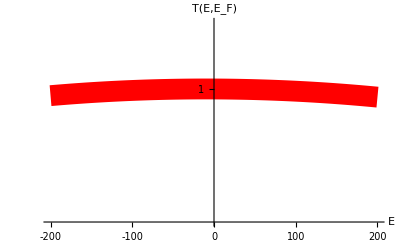

```mathematica
A8=Plot[{(Abs[Te]^2+Abs[Th]^2)/.{Gf->10,GM->0,γ->0,ϕ->1.57}},{G,-200,200},PlotRange->{{-200,200},{0.98,1.01}},PlotStyle->{Directive[AbsoluteThickness[15],Opacity[1],Red]},Ticks->{{-200,-100,0,100,200},{0,0.5,1}},PlotPoints->10,AxesLabel->{Framed[Style["E",25,AbsoluteThickness[15],Black],FrameStyle->None,FrameMargins->10],Framed[Style["T(E,E_F)",25,AbsoluteThickness[15],Black],FrameStyle->None,FrameMargins->10]},Ticks->{{-200,-100,0,100,200},{0.98,0.99,1}},TicksStyle->Directive[Black,10]]
```